# Just launch the code below to run the notebook (shift+enter)

```mathematica
ClearAll["Global`*"]
ParallelEvaluate[ClearAll["Global`*"]];
BlockEvaluation[tag_]:=Block[{},
nb=EvaluationNotebook[];
NotebookFind[nb,tag,All,CellTags];
SelectionEvaluate[nb]
]
CloseKernels[];
LaunchKernels[];
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
infoDialog[phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],Button["Proceed",DialogReturn[choice]]}]]
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Auxiliary data"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Auxiliary data"}]]];
choiceslist={"Tabulated Nevents+sensitivity","Sensitivity only (tabulated Nevents must be produced before)","Acceptance"};
taglist["Acceptance"]="Acceptance";
taglist["Tabulated Nevents+sensitivity"]="Number-of-events+sensitivity";
taglist["Sensitivity only (tabulated Nevents must be produced before)"]="Sensitivity";
computationchoice=dropdownDialog[choiceslist,"Do you want to compute the tabulated number of events and then sensitivity, or just sensitivity (if the tabulated number of events has been already produced)?"];
tagselected=taglist[computationchoice]
BlockEvaluation[tagselected]
```

Number-of-events+sensitivity

# Preliminary definitions

## Various directories

```mathematica
LLPdirName="ALP-fermion";
(*Set the directory for the search where tabulated acceptances are located*)
directory["Acceptances"]=FileNameJoin[{NotebookDirectory[],"Acceptances"}];
(*Set the directory for the search where tabulated angle-energy distributions are located*)
directory["Distribution"]=FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra",LLPdirName}]; 
(*The directory storing production weights of the given LLP*)
directory["Production weights"]=FileNameJoin[{NotebookDirectory[],"phenomenology",LLPdirName,"Production probabilities"}]; 
(*Directory to which various auxillary datasets will be stored*)
directory["Auxiliary"]=FileNameJoin[{NotebookDirectory[],"Auxiliary data",LLPdirName}]; 
If[!DirectoryQ[directory["Auxiliary"]],CreateDirectory[directory["Auxiliary"]]];
(*Directory containing decay widths of the LLPs*)
directory["Decays"]=FileNameJoin[{NotebookDirectory[],"phenomenology",LLPdirName,"decay widths"}];
```

## Parameters and various functions

```mathematica
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
infoDialog[phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],Button["Proceed",DialogReturn[choice]]}]]
selectionDialog[list_,phrase_]:=DialogInput[{choice={}},Column[{Row[{"Select the experiments for which the number of events will be computed:"}],Pane[TogglerBar[Dynamic[choice],list,Appearance->"Vertical"->{Automatic,5}],ImageSize->{Automatic,Automatic},Scrollbars->{False,True}],Button["OK",DialogReturn[choice]]}]]
(*chbar*)
chbar= 6.6*10^-25*3*10^8;
(*Decay width of mesons*)
τπ0=8.52*10^-17;
Γπ0=chbar/τπ0;
τB=1.64*10^-12;
hbar=6.58*10^-25;
ΓBdecayGeV=hbar/τB;
(*Bare quark masses from pdg*)
md=4.67*10^-3;
mu=2.16*10^-3;
ms=0.093;
(*Scales*)
ΛwVal=80;
ΛQCDval=0.34;
(*Coupling constants*)
αEM=1/137;
αW=1/29.;
fπ=0.093;
θηηpr=ArcSin[-1/3.];
(*Cross-sections*)
σpNucleonInpb[Atarget_]=If[Atarget==1., 42.5*10^(9),51*Atarget^-0.29*10^9];  (*The first case is for SHIFT target*)
σppLHC=72*10^9;
(*Masses of various SM particles*)
{mSM["Bplus"],mSM["Kplus"],mSM["PiPlus"],mSM["h"],mSM["Bs"]}={5.279,0.495,0.139,62.5,5.366};
(*αS[ma_] = Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/AlphaS.txt"}],"Table"],InterpolationOrder->1][ma];*)
(*____________________*)
(*B/K fragmentation fractions*)
(*____________________*)
(*Fragmentation fractions at the LHC. For the moment, the same fractions are assumed to be at the FCC-hh*)
fbtob0["LHC"]=fbtobplus["LHC"]=fbtob0["FCC-hh"]=fbtobplus["FCC-hh"]=0.324;
fbtobs["LHC"]=fbtobs["FCC-hh"]=0.09;
(*Fragmentation fractions at SPS. From SHiP physics paper*)
fbtobs["SPS"]=0.11;
fbtob0["SPS"]=fbtobplus["SPS"]=0.411;
fstokplus["SPS"]=0.5;
fstok0l["SPS"]=0.25;
(*Fraction of K^(+/-) decaying in-flight at SPS, from https://arxiv.org/pdf/2004.07974.pdf*)
fractionDecayInFlightKplusKminus=(0.29+0.07);
(*Fragmentation fractions at FermilabBD. Assumed to be the same as at SPS*)
fbtobs["FermilabBD"]=0.11;
fbtob0["FermilabBD"]=fbtobplus["FermilabBD"]=0.411;
(*Fragmentation fractions at Serpukhov. Assumed to be zero*)
fbtobs["Serpukhov"]=0.;
fbtob0["Serpukhov"]=fbtobplus["Serpukhov"]=0.;

(*Fragmentation fractions at LHC fixed target*)
(*Calculated for c quarks and estimated for b quarks*)
fbtobplus["LHC-fixed-target"]=0.4;
fbtob0["LHC-fixed-target"]=0.4;
fbtobs["LHC-fixed-target"]=0.1; 
(*copied for SPS*)
fstokplus["LHC-fixed-target"]=0.5;
fstok0l["LHC-fixed-target"]=0.25;
```

## LLP phenomenology: prodution probabilities, decay widths (y = 2v_h/f_a)

## Scanning for tabulated distributions

```mathematica
(*Define the file pattern*)
pattern="DoubleDistr_*_*_*.m";
(*Search for files matching the pattern in the directory and its subdirectories*)
matchingFiles=FileNames[pattern,{directory["Distribution"]},Infinity];
(*List of LLPs, production modes, and facilities for which the tabulated distributions have been computed at the previous stage of using SensCalc*)
ExtractedProductionParameters=Function[filename,parts=StringSplit[FileNameTake[filename],"_"];
{parts[[2]],parts[[3]],StringDrop[parts[[4]],-2]} ];
(*combinations selected LLP, production channel, facility for which the tabulated distributions are present*)
DistrCombinations=(ExtractedProductionParameters/@matchingFiles)//Sort
Print["Phenomenology choice:"]
phen=dropdownDialog[{"Revised","Old"},"Use the revised phenomenology (2310.03524), or the old one (1901.09966; no hadronic decays, production only via B->K/K*)? Must be consistent with the choice made in 1. Acceptances.nb"];
If[phen==Null,phen="Revised"];
phen
If[phen=="Old",DistrCombinations=Select[DistrCombinations,#[[2]]=="B"&]]
```

(ALP-fermion | B | FermilabBD
ALP-fermion | B | LHC
ALP-fermion | B | LHC-fixed-target
ALP-fermion | B | SPS
ALP-fermion | DrellYan | FermilabBD
ALP-fermion | DrellYan | LHC
ALP-fermion | DrellYan | SPS
ALP-fermion | Eta | FermilabBD
ALP-fermion | Eta | LHC
ALP-fermion | Eta | LHC-fixed-target
ALP-fermion | Eta | SPS
ALP-fermion | EtaPr | FermilabBD
ALP-fermion | EtaPr | LHC
ALP-fermion | EtaPr | LHC-fixed-target
ALP-fermion | EtaPr | SPS
ALP-fermion | Pi0 | FermilabBD
ALP-fermion | Pi0 | LHC
ALP-fermion | Pi0 | LHC-fixed-target
ALP-fermion | Pi0 | SPS)

Phenomenology choice:

Revised

## Production probabilities

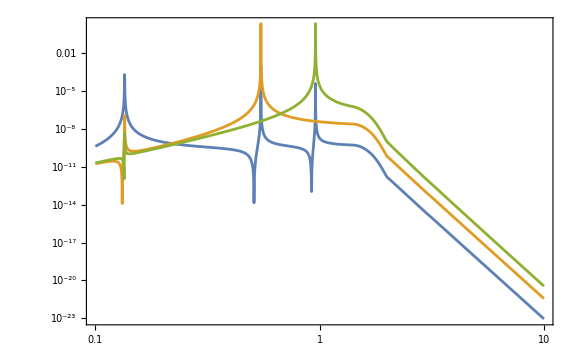

Import::nffil: File /Users/jeremi/Documents/Physics/SHIFT/SensCalc.nosync/phenomenology/ALP-fermion/Production probabilities/sigmaDrellYan_ALP-fermion_LHC-fixed-target.txt not found during Import.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Interpolation::innd: First argument in $Failed does not contain a list of data and coordinates.

If there are production weights to all available distributions:

True

```mathematica
ProductionProbabilitiesCoefs=Import[FileNameJoin[{directory["Production weights"],"Coefs-production-Fermion universal-scale-1000.-GeV.m"}],"MX"];
vh=246.;
{θam02["Pi0",ma_,y_],θam02["Eta",ma_,y_],θam02["EtaPr",ma_,y_],BrBtoALPtotal[ma_,y_],cGGeff[ma_,y_],BrBtoALPKplus[ma_,y_],BrBtoALPKstar[ma_,y_]}=ProductionProbabilitiesCoefs/.{f->(2vh)/y};
LogLogPlot[Evaluate[{θam02["Pi0",ma,1],θam02["Eta",ma,1],θam02["EtaPr",ma,1]}],{ma,0.1,10},Frame->True,ImageSize->Large]
FacilitiesList={"SPS","FermilabBD","LHC","FCC-hh","Serpukhov","ESS", "LHC-fixed-target"};
Do[
PmotherToLLP[mLLP_,y_,part,Facility]=If[phen=="Revised",θam02[part,mLLP,y],0.];
,{part,{"Pi0","Eta","EtaPr"}},{Facility,FacilitiesList}]
Do[
PmotherToLLP[mLLP_,y_,"B",Facility]=(fbtob0[Facility]+fbtobplus[Facility])If[phen=="Revised",BrBtoALPtotal[mLLP,y],BrBtoALPKplus[mLLP,y]+BrBtoALPKstar[mLLP,y]];
,{Facility,FacilitiesList}]

(*Production from Drell-Yan process*)
σDrellYanData[Facility_]:=Block[{},
dat=Import[FileNameJoin[{directory["Production weights"],"sigmaDrellYan_ALP-fermion_"<>Facility<>".txt"}],"Table"];
MinMaxMassesDrellYan[Facility]={Min[dat[[All,1]]],Min[4,Max[dat[[All,1]]]]};
int[ma_]=If[MinMaxMassesDrellYan[Facility][[1]]≤ ma≤MinMaxMassesDrellYan[Facility][[2]],Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]+10^-90]}&/@dat,InterpolationOrder->1][Log10[ma]])],0];
PmotherToLLP[mLLP_,y_,"DrellYan",Facility]=Abs[cGGeff[mLLP,y]]^2*int[mLLP]/σpNucleonInpb[Atarget]
]
Do[σDrellYanData[Facility],{Facility,{"SPS","FermilabBD","LHC", "LHC-fixed-target"}}]
WeightsCombinations=Cases[Keys[DownValues@PmotherToLLP][[All,1,#]]&/@{3,4}//Transpose//Sort,_?(MemberQ[DistrCombinations[[All,{2,3}]],#]&)];
Print["If there are production weights to all available distributions:"]
IfCondDistrToWeights=DistrCombinations[[All,{2,3}]]==WeightsCombinations
If[!IfCondDistrToWeights,infoDialog["You have not provided the production probabilities PmotherToLLP to all the generated tabulated distributions! Please do this first to avoid problems"];]
```

## LLP lifetime and branching ratios

### Lifetimes and branching ratios

```mathematica
(*List of widths of the ALP into various final states*)
DecayWidthsDataTemp=Import[FileNameJoin[{directory["Decays"],"Widths-model-Fermion universal-scale-1000.-GeV.m"}],"MX"];
DecayWidthsDataTemp2=DecayWidthsDataTemp[[4]];
{Table[i,{i,1,Length[DecayWidthsDataTemp2[[1]]],1}],DecayWidthsDataTemp2[[1]]}//TableForm
DecayWidthsData=Drop[DecayWidthsDataTemp2,3];
(*Total decay width and lifetime*)
totalwidthdata=If[phen=="Revised",DecayWidthsData[[All,{1,-1}]],Join[DecayWidthsData[[All,{1}]],DecayWidthsData[[All,{2}]]+DecayWidthsData[[All,{4}]]+DecayWidthsData[[All,{5}]],2]];
ΓLLP[mLLP_,y_]=(1/(2vh))^2 y^2 Interpolation[totalwidthdata,InterpolationOrder->1][mLLP];
cτLLP[mLLP_,y_]=chbar/ΓLLP[mLLP,y];
ldecayLLP[mLLP_,y_,ELLP_]=cτLLP[mLLP,y](√(ELLP^2-mLLP^2))/mLLP;
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34
m_a, GeV | 2e | 2γ | 2μ | 2τ | 2b | 2c | 2d | 2G | 2s | 2t | 2u | 2π^+2π^- | 2ϕ | 2ω | 3π^0 | 3η | K^(*0)(K̄)^(*0) | K^0(K̄)^0π^0 | K^(*+)K^(*-) | K^-K^0π^+ | K^+K^-π^0 | K^+(K̄)^0π^- | γπ^+π^- | η2π^0 | ηπ^+π^- | π^+π^-2π^0 | π^+π^-π^0 | ωπ^+π^- | η'2π^0 | η'π^+π^- | Non-hadronic, total | Hadronic, total | Total

## Loading necessary routines

```mathematica
If[Length[inecessary]==0,
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"codes/generic.nb"}]];
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"codes/for-sensitivities.nb"}]];
inecessary={1,2,3};
]
```

# Specifying the experiments

```mathematica
SetDirectory[NotebookDirectory[]];
(*Parent directory*)
NotebookDirectory[]//ParentDirectory;
ExperimentDirectoriesList=Select[FileNames["*",directory["Acceptances"],1],DirectoryQ];
(*List of available experiments (for which the geometry has been implemented)*)
ExperimentsListTemp=Table[FileNameTake[ExperimentDirectoriesList[[i]],-1],{i,1,Length[ExperimentDirectoriesList],1}];
ExperimentsListTemp2=Join[Partition[ExperimentsListTemp,1],Table[{TrueQ@FileExistsQ@FileNameJoin[{directory["Acceptances"],ExperimentsListTemp[[i]],ToString@StringForm["Acceptance_``_for_``.m",Sequence@@{ExperimentsListTemp[[i]],LLPdirName}]}]},{i,1,Length[ExperimentsListTemp]}],2];
ExperimentsList=Select[ExperimentsListTemp2,#[[2]]==True&][[All,1]]//Sort
If[Length[ExperimentsList]==0,Print["No experiment is available, generate first the acceptance for the given experiment using module 1"]]
Print["Selected experiments:"]
SelectedExperimentList=If[Length[ExperimentsList]≠0,selectionDialog[ExperimentsList,"Select the experiments:"]]
icounter=1;
```

{CODEX-b,DarkQuest-phase-2,FACET,SHIFT-muon,SHiP-ECN4}

Selected experiments:

{FACET}

## Running block for next sections

```mathematica
BlockEvaluation[tag_]:=Block[{},
nb=EvaluationNotebook[];
NotebookFind[nb,tag,All,CellTags];
SelectionEvaluate[nb]
]
If[tagselected=="Number-of-events+sensitivity",
Do[
BlockEvaluation["Number-of-events-computation+sensitivity"];
,{icounter,1,Length[SelectedExperimentList],1}],
If[tagselected=="Acceptance",
Do[
BlockEvaluation["Acceptance-computation"];
,{icounter,1,Length[SelectedExperimentList],1}]
]
]
```

# Number of events

## Particular experiment

```mathematica
SelectedExperiment=SelectedExperimentList[[icounter++]];
```

## Cross-sections, acceptances

{0.384673,Null}

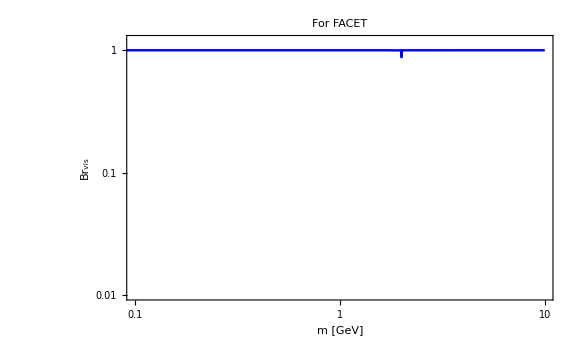

χ_(b  or  OverscriptBox[b, _]) | χ_(π^0) | χ_η | χ_η'
0.0172222 | 42.8 | 4.7 | 0.5

Search for ALP-fermion at FACET located at LHC. N_collisions = 2.16×10^17

Quantity | θ_min, rad | θ_max, rad | θ_min(ϵ_dec), rad | θ_max(ϵ_dec), rad | z_min, m | z_max, m
Description | Min angle covered by experiment | Max angle covered by experiment | Min angle where ϵ_decay≠0 | Max angle where ϵ_decay≠0 | Min long. displacement of the decay volume | Max long. displacement of the decay volume
Value | 0.0034589 | 0.0058983 | 0.0034589 | 0.0058983 | 101. | 119.

```mathematica
dataAcceptances=Import[FileNameJoin[{FileNameJoin[{directory["Acceptances"],SelectedExperiment,ToString@StringForm["Acceptance_``_for_``.m",Sequence@@{SelectedExperiment,LLPdirName}]}]}],"MX"];//AbsoluteTiming
{FacilityGivenExperiment,FullAcceptanceData0,BrVis[mLLP_]}=dataAcceptances[[#]]&/@{1,3,5};
LogLogPlot[Evaluate[BrVis[mLLP]],{mLLP,0.02,10},Frame->True,ImageSize->Large,FrameStyle->Directive[Black, 22],PlotStyle->{{Thickness[0.003],Blue},{Thickness[0.003],Darker@Red},{Thickness[0.003],Darker@Darker@Green},{Thickness[0.003],Black}},GridLines->Automatic,PlotRange->{{0.1,10},{0.01,1.2}},Frame->True,ImageSize->Large,FrameLabel->{"m [GeV]","Br_vis"},PlotLabel-> Style[Row[{"For ",SelectedExperiment}], 20, Black]]
(*___________________________*)
(*Interpolation of the tabulated azimuthal acceptance, extracting Subscript[θ, min/max], etc.*)
(*___________________________*)
{AzimuthalAcceptanceInt[θLLP_,zLLP_],θminExpAll,θmaxExpAll,θminExp,θmaxExp,zminExp,zmaxExp,zminθ[θLLP_],zmaxθ[θLLP_]}=BlockϵAzimuthal[FullAcceptanceData0];
(*Logarithmized data with full acceptance, and also decay acceptance and full acceptance interpolations*)
{FullAcceptanceData,DecayAcceptanceInt[mLLP_,θLLP_,ELLP_,zLLP_],FullAcceptanceInt[mLLP_,θLLP_,ELLP_,zLLP_],InGridmϵ,InGridθϵ,InGridEϵ,InGridzϵ,ϵvals,ϵazvals,mminϵ,mmaxϵ}=BlockϵDecay[FullAcceptanceData0,zminExp,BrVis];
CrossSectionData=dataAcceptances[[4]]//Transpose;
NpotGivenExperiment=Select[CrossSectionData,#[[1]]=="Npot"&][[1]][[2]]//N;
ProbMother["B"]=Select[CrossSectionData,#[[1]]=="Pb"&][[1]][[2]];
ProbMother["Pi0"]=Select[CrossSectionData,#[[1]]=="PPi0"&][[1]][[2]];
ProbMother["Eta"]=Select[CrossSectionData,#[[1]]=="PEta"&][[1]][[2]];
ProbMother["EtaPr"]=Select[CrossSectionData,#[[1]]=="PEtapr"&][[1]][[2]];
ProbMother["DrellYan"]=1.;
AtargetVal=Select[CrossSectionData,#[[1]]=="Atarget"&][[1]][[2]];
{{"χ_(b  or  OverscriptBox[b, _])","χ_(π^0)","χ_η","χ_η'"},{ProbMother["B"],ProbMother["Pi0"],ProbMother["Eta"],ProbMother["EtaPr"]}}//TableForm
(*infoDialog[Row[{"The number of proton collisions is ", NpotGivenExperiment,". You may change it at the stage of computing the sensitivities"}]]*)
Row[{"Search for "<>LLPdirName <>" at ", SelectedExperiment, " located at ",FacilityGivenExperiment,". N_collisions = ",NpotGivenExperiment}]
{{"Quantity","θ_min, rad","θ_max, rad","θ_min(ϵ_dec), rad","θ_max(ϵ_dec), rad","z_min, m","z_max, m"},{"Description","Min angle covered by experiment","Max angle covered by experiment","Min angle where ϵ_decay≠0","Max angle where ϵ_decay≠0","Min long. displacement of the decay volume","Max long. displacement of the decay volume"},{"Value",θminExpAll,θmaxExpAll,θminExp,θmaxExp,zminExp,zmaxExp}}//TableForm
```

## Angle-energy distributions for the given experiment

Production list:

{B,DrellYan,Eta,EtaPr,Pi0}

{0.333228,Null}

{12.5977,Null}

InterpolatingFunction::dmval: Input value {0.1,-2.46106} lies outside the range of data in the interpolating function. Extrapolation will be used.

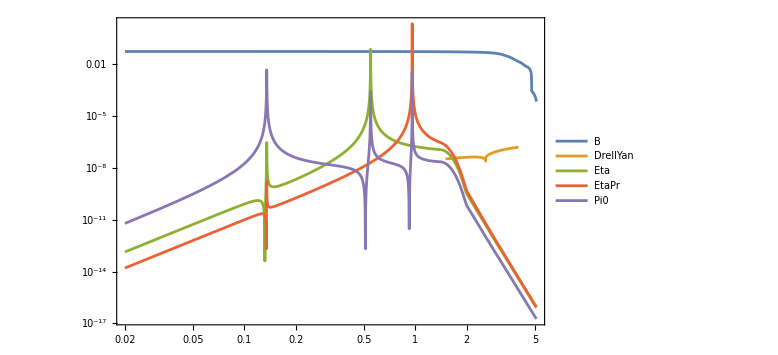
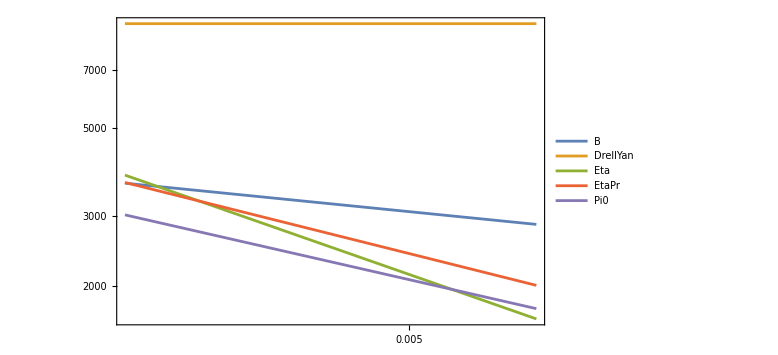

```mathematica
ProductionPatternSelected=Select[DistrCombinations,#[[3]]==FacilityGivenExperiment&];
Print["Production list:"]
ProductionList=ProductionPatternSelected[[All,2]]//DeleteDuplicates
Do[
Module[{prod},
prod=ProductionPatternSelected[[i]][[2]];
(*Importing the data with distribution*)
dirimp=If[prod=="DrellYan",FileNameJoin[{directory["Distribution"],"Pregenerated"}],directory["Distribution"]];
DistrDataImport[prod]=Import[FileNameJoin[{dirimp,"DoubleDistr_"<>LLPdirName<>"_"<>prod<>"_"<>FacilityGivenExperiment<>".m"}],"MX"];
If[prod=="DrellYan",
DistrDataImport[prod]=Select[DistrDataImport[prod],MinMaxMassesDrellYan[FacilityGivenExperiment][[1]]<=#[[1]]<=MinMaxMassesDrellYan[FacilityGivenExperiment][[2]]&];
];
(*Min/mass mass of the LLP from the data*)
mlistDistr[prod]=DeleteDuplicates[DistrDataImport[prod][[All,1]]];
{mLLPmin[prod],mLLPmax[prod]}=MinMax[mlistDistr[prod]];
(*Interpolation of the tabulated distribution*)
DoubleDistrLLPint[mLLP_,θLLP_,ELLP_,prod]=10^(Interpolation[distrlogComp[DistrDataImport[prod]],InterpolationOrder->1][Log10[mLLP],Log10[θLLP],Log10[ELLP]]);
(*Probability to produce LLP*)
ProbLLP[mLLP_,finv_,prod]=ProbMother[prod]*PmotherToLLP[mLLP,finv,prod,FacilityGivenExperiment]/.{Atarget->AtargetVal};
]
,{i,1,Length[ProductionPatternSelected],1}]
directory["Auxiliary-experiment"]=FileNameJoin[{directory["Auxiliary"],SelectedExperiment}];
If[!DirectoryQ[directory["Auxiliary-experiment"]],CreateDirectory[directory["Auxiliary-experiment"]]];
Export[FileNameJoin[{directory["Auxiliary-experiment"],"Double-Distr-Averaged-"<>LLPdirName<>".m"}],{Sum[If[mLLPmin[prod]<mLLP<mLLPmax[prod],Evaluate[ProbLLP[mLLP,1,prod]],0],{prod,ProductionList}],(1/Sum[If[mLLPmin[prod]<mLLP<mLLPmax[prod],Evaluate[ProbLLP[mLLP,1,prod]],0],{prod,ProductionList}])Sum[If[mLLPmin[prod]<mLLP<mLLPmax[prod],Evaluate[ProbLLP[mLLP,1,prod]*DoubleDistrLLPint[mLLP,θLLP,ELLP,prod]],0],{prod,ProductionList}]},"MX"];
Do[{GridInFinal[prod],DistrVals[prod]}=BlockGridsValsDistr[prod,DistrDataImport],{prod,ProductionList}];//AbsoluteTiming
(*____________________________*)
(*Finding Subscript[E, max](Subscript[m, LLP],Subscript[θ, LLP]) for the angular range at the given experiment*)
(*____________________________*)
Do[ELLPmax[mfip_,θfip_,prod]=EmaxBlock[prod,9,DistrDataImport,FacilityGivenExperiment],{prod,Select[ProductionList,#!="Bremsstrahlung"&]}]//AbsoluteTiming
(*Temporary fix for ALPs from mixing*)
If[SelectedExperiment=="NuCal",
Do[ELLPmax[mfip_,θfip_,prod]=70.,{prod,Select[ProductionList,#!="Bremsstrahlung"&]}]];
If[SelectedExperiment=="NA62-dump",
Do[ELLPmax[mfip_,θfip_,prod]=400.,{prod,Select[ProductionList,#!="Bremsstrahlung"&]}]];
ptenergies=LogLogPlot[Evaluate[Table[ELLPmax[0.1,θLLP,prod],{prod,ProductionList}]],{θLLP,θminExp,θmaxExp},Frame->True,ImageSize->Large,PlotLegends->Placed[Style[#,15]&/@ProductionList,Right]];
ptprodprob=LogLogPlot[Evaluate[Table[ProbLLP[ma,1,prod],{prod,ProductionList}]],{ma,mminϵ,mmaxϵ},Frame->True,ImageSize->Large,PlotLegends->Placed[Style[#,15]&/@ProductionList,Right]];
Style[Row[{ptprodprob,ptenergies}],ImageSizeMultipliers->{1, 1}]
```

## Number of events

## Number of events - using the mapping method

### Initializing all routines

```mathematica
Do[{OutGridθfinal[prod],Δθvals[prod]}=OutGridθTemp[InGridθϵ,30,prod,θmaxBrem],{prod,ProductionList}]
{OutGridzfinal,Δzvals}=OutGridszTemp[InGridzϵ,30,zminExp];
(*Final energy grid. Mass- and production channel-dependent*)
If[FacilityGivenExperiment!="ESS",
StepEtemp[Efip_]=Piecewise[{{0.3,Efip≤2.5},{0.5,2.5<Efip<35},{2,35≤Efip≤50},{4,50<Efip<160},{5,160≤Efip<=400},{25,400<Efip<600},{50,600<=Efip<2000},{200,2000≤Efip<4000},{400,4000≤Efip<7000},{500,7000≤Efip≤50000}}];
OutGridEnergy[m_,ProdChannel_]:=Block[{},
emin=If[ProdChannel!="Bremsstrahlung",1.0m,ELLPmin["Bremsstrahlung"]];
egridtemp=With[{start=emin,end=ELLPmax[m,θminExp,ProdChannel]},
Log10[NestWhileList[#+StepEtemp[#]&,start,#≤end&,1,∞,-1]]]//N;
If[Length[egridtemp]==1,egridtemp=Join[egridtemp,{Log10[2*emin]}]];
egridtemp
]
,
StepEtemp[Efip_]=0.001;
OutGridEnergy[m_,ProdChannel_]:=Block[{},
tabt=Table[e,{e,1.0001m,ELLPmax[m,θminExp,ProdChannel],0.001}];
If[Length[tabt]==1,tabt=Join[tabt,{ELLPmax[m,θminExp,ProdChannel]}]//Sort//DeleteDuplicates];
Log10[tabt]//N
]
]
(*Block that computes the grid Subscript[θ, S],Subscript[E, S],Subscript[z, S], Subscript[ϵ, Full]×Subscript[f, Subscript[θ, S],Subscript[E, S]]*)
TableIntegrandDiscret[m_,ProdChannel_,ϵDecOp_]:=TableIntegrandDiscretTemp[m,ProdChannel,ϵDecOp,ϵvals,ϵazvals,OutGridθfinal[ProdChannel],OutGridzfinal,OutGridEnergy,InGridmϵ,InGridθϵ,InGridEϵ,InGridzϵ,Δθvals[ProdChannel],Δzvals,zminExp,GridInFinal,DistrVals,FacilityGivenExperiment]
```

### Generalized acceptances

{3.86056,Null}

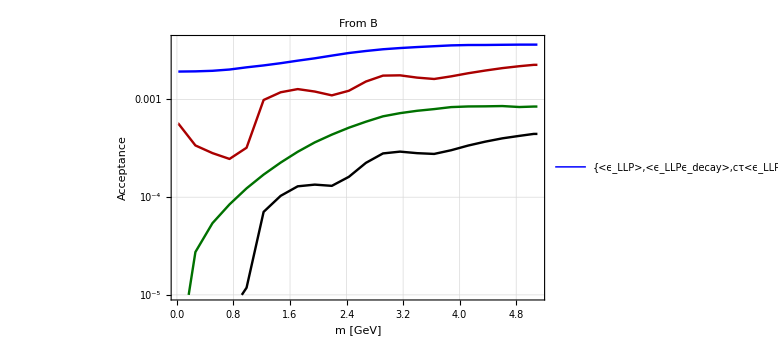
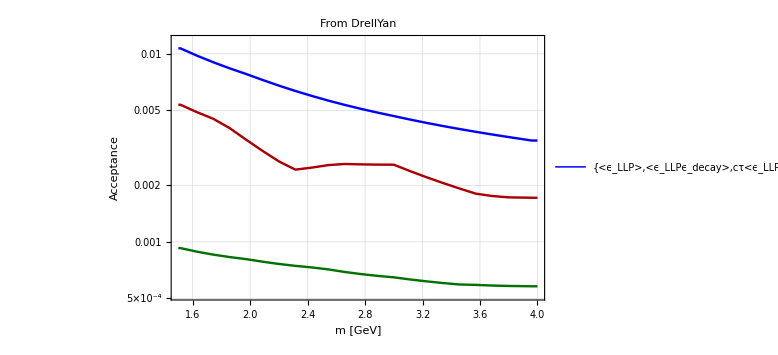
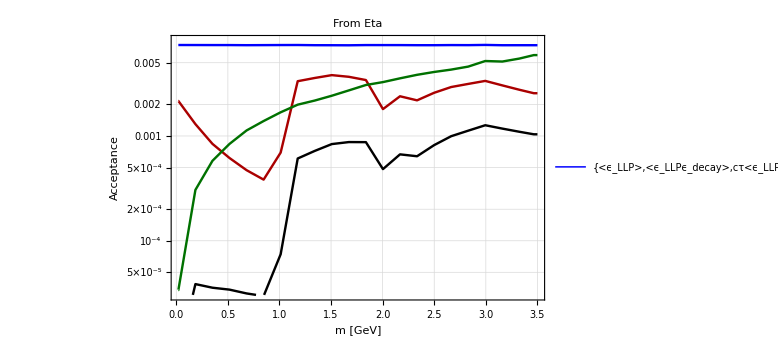
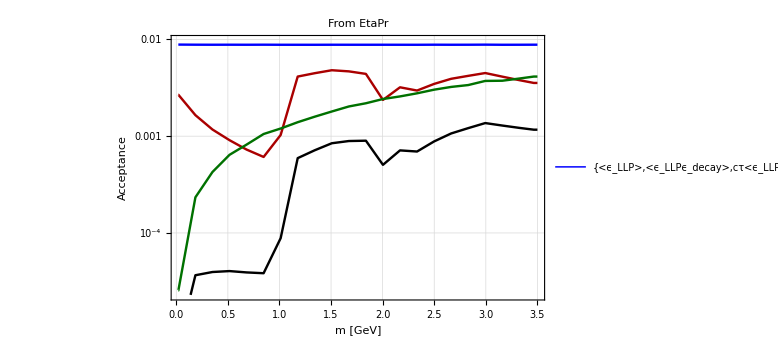
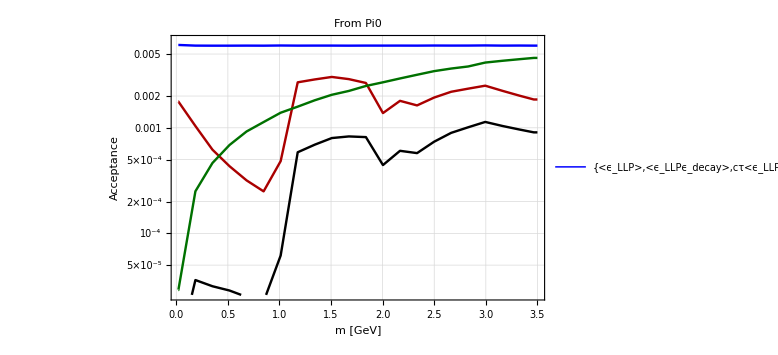

```mathematica
(*Tabulated acceptance*)
FactorANUBISceiling=If[SelectedExperiment=="ANUBIS-ceiling",2,1];
AcceptanceDiscret[m_,ProdChannel_,ϵdecOp_,decProb_]:=AcceptanceDiscretTemp[m,ProdChannel,ϵdecOp,decProb,mLLPmin,mminϵ,mLLPmax,mmaxϵ,ELLPmax,θminExp,TableIntegrandDiscret,BrVis,zmaxExp,zminExp,FactorANUBISceiling,0.]
Do[mlistAcceptance[prod]=Join[Table[m,{m,1.01Max[mLLPmin[prod],mminϵ],0.95Min[mLLPmax[prod],mmaxϵ],Min[(0.95Min[mLLPmax[prod],mmaxϵ]-1.01Max[mLLPmin[prod],mminϵ])/20,2]}],{0.99Min[mLLPmax[prod],mmaxϵ]}],{prod,ProductionList}];
Do[
ϵGeomTabs[prod]=ParallelTable[{m,AcceptanceDiscret[m,prod,"False",0],AcceptanceDiscret[m,prod,"True",0],AcceptanceDiscret[m,prod,"False",1],AcceptanceDiscret[m,prod,"True",1]},{m,mlistAcceptance[prod]}];
ϵGeomTabs[prod]=Join[{Join[{Max[mLLPmin[prod],mminϵ]},Drop[ϵGeomTabs[prod][[1]],1]]},ϵGeomTabs[prod],{Join[{Min[mLLPmax[prod],mmaxϵ]},Drop[ϵGeomTabs[prod][[-1]],1]]}];
,{prod,ProductionList}];//AbsoluteTiming
PlotAcc[ProdChannel_]:=ListLogPlot[Evaluate[{ϵGeomTabs[ProdChannel][[All,{1,2}]],ϵGeomTabs[ProdChannel][[All,{1,3}]],ϵGeomTabs[ProdChannel][[All,{1,4}]],ϵGeomTabs[ProdChannel][[All,{1,5}]]}],FrameStyle->Directive[Black, 22],PlotStyle->{{Thickness[0.003],Blue},{Thickness[0.003],Darker@Red},{Thickness[0.003],Darker@Darker@Green},{Thickness[0.003],Black}},GridLines->Automatic,PlotRange->{MinMax[ϵGeomTabs[ProdChannel][[All,1]]],{Max[0.9Min[Min[ϵGeomTabs[ProdChannel][[All,4]]],Min[ϵGeomTabs[ProdChannel][[All,3]]]],10^-5],1.1Max[Max[ϵGeomTabs[ProdChannel][[All,2]]],Max[ϵGeomTabs[ProdChannel][[All,4]]]]}},Joined->True,Frame->True,ImageSize->Large,FrameLabel->{"m [GeV]","Acceptance"},PlotLabel-> Style[Row[{"From ",ProdChannel}], 20, Black],PlotLegends->Placed[{Style[#, 18]&/@{"<ϵ_LLP>","<ϵ_LLPϵ_decay>","cτ<ϵ_LLPP_decay>","cτ<ϵ_LLPP_decayϵ_decay>"}},{0.75,0.2}]]
Style[Row[Evaluate[Table[PlotAcc[prod],{prod,ProductionList}]]],ImageSizeMultipliers->{1,1,1,1}]
(*Do[FilenameAcceptance[prod]=ToString@StringForm["Acceptance_ALP-fermion_at_``_From_``.dat",Sequence@@{SelectedExperiment,ExportList[prod]}];
Export[FileNameJoin[{NotebookDirectory[],"Auxiliary data/ALPs with fermion coupling",SelectedExperiment,FilenameAcceptance[prod]}],ϵGeomTabs[prod][[All,{1,2,4,5}]],"Table"]
,{prod,ProductionList}]*)
AccAveraged[mLLP_,cτ_]=NpotGivenExperiment{Sum[If[mLLPmin[prod]<mLLP<mLLPmax[prod],Evaluate[ProbLLP[mLLP,1,prod]],0],{prod,ProductionList}],Sum[If[Max[mLLPmin[prod],mminϵ]<mLLP<Min[mLLPmax[prod],mmaxϵ],Evaluate[ProbLLP[mLLP,1,prod]*Interpolation[ϵGeomTabs[prod][[All,{1,2}]],InterpolationOrder->1][mLLP]],0],{prod,ProductionList}],Sum[If[Max[mLLPmin[prod],mminϵ]<mLLP<Min[mLLPmax[prod],mmaxϵ],Evaluate[ProbLLP[mLLP,1,prod]/cτ*Interpolation[ϵGeomTabs[prod][[All,{1,4}]],InterpolationOrder->1][mLLP]],0],{prod,ProductionList}],Sum[If[Max[mLLPmin[prod],mminϵ]<mLLP<Min[mLLPmax[prod],mmaxϵ],Evaluate[ProbLLP[mLLP,1,prod]/cτ*Interpolation[ϵGeomTabs[prod][[All,{1,5}]],InterpolationOrder->1][mLLP]],0],{prod,ProductionList}]};
Export[FileNameJoin[{directory["Auxiliary-experiment"],"AcceptanceAveraged-"<>LLPdirName<>".m"}],AccAveraged[mLLP,cτ],"MX"];
```

### Rough estimates of the upper and lower bounds

#### Definitions

InterpolatingFunction::dmval: Input value {0.5,-2.46106} lies outside the range of data in the interpolating function. Extrapolation will be used.

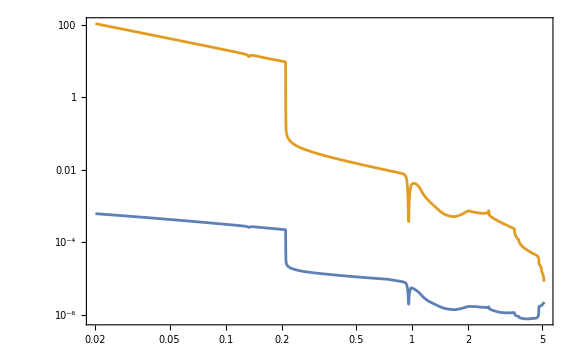

```mathematica
Do[LowerBoundEstimate[mLLP_,prod]=((NpotGivenExperiment*ProbLLP[mLLP,1,prod]*Interpolation[ϵGeomTabs[prod][[All,{1,5}]],InterpolationOrder->1][mLLP])/(2.3ldecayLLP[mLLP,1,ELLP] mLLP/(√(ELLP^2-mLLP^2))))^(-1/4);
UpperBoundEstimate[mLLP_,prod]=(Abs[Re[Evaluate[-ProductLog[-1,-2.3*b/a]/b/.{a-> NpotGivenExperiment*ProbLLP[mLLP,1,prod]*Interpolation[ϵGeomTabs[prod][[All,{1,3}]],InterpolationOrder->1][mLLP],b->zminExp/ldecayLLP[mLLP,1,ELLPmax[0.5,θminExp,prod]]}]]])^(1/2),{prod,ProductionList}]
ProdTest=ProductionList[[1]];
LogLogPlot[Evaluate[{0.3LowerBoundEstimate[mLLP,ProdTest],1.8UpperBoundEstimate[mLLP,ProdTest]}],{mLLP,Max[mLLPmin[ProdTest],mminϵ],Min[mLLPmax[ProdTest],mmaxϵ]},Frame->True,ImageSize->Large]
```

### Number of events - fast

```mathematica
FactorLowerBound=If[MemberQ[{"ANUBIS-shaft-volume-1","ANUBIS-shaft-volume-2","ANUBIS-shaft-volume-3"},SelectedExperiment]==True,0.1,0.3];
NeventsDiscret[m_,ProdChannel_,couplinglist_]:=Module[{NevDiscret,NpotTimesχval,zshift},
If[Max[mLLPmin[ProdChannel],mminϵ]<m<Min[mLLPmax[ProdChannel],mmaxϵ],
integrandtab=TableIntegrandDiscret[m,ProdChannel,"True"];
NpotTimesχval[coupling_]=NpotGivenExperiment*ProbLLP[m,coupling,ProdChannel];
{lowerbound,upperbound}={LowerBoundEstimate[m,ProdChannel],UpperBoundEstimate[m,ProdChannel]};
brvis=BrVis[m];
NevDiscret[coupling_]:=If[0.1lowerbound<coupling<(*1.5*)2upperbound,NpotTimesχval[coupling]*brvis*sumcompile[tableprefac[integrandtab,m,cτLLP[m,coupling],1,0.]],0.];
Table[{m,couplinglist[[i]],NevDiscret[couplinglist[[i]]]},{i,1,Length[couplinglist],1}],Table[{m,couplinglist[[i]],0.},{i,1,Length[couplinglist],1}]]
]
```

### Number of events - slow (using built-in Mathematica functions Interpolation, NIntegrate)

```mathematica
(*Differential decay probability 1/ldecay Exp[-l/ldecay], where l is expressed in terms of the longitudinal displacement z and polar angle θ as z/cosθ*)
(*Differential decay probability (1/ldecay)Exp[-l/ldecay], where l is expressed in terms of the longitudinal displacement z and polar angle θ as z/cosθ*)
PdecayDensity[mLLP_,coupling_,θLLP_,ELLP_,zLLP_]=Exp[-zLLP/(Cos[θLLP]*ldecayLLP[mLLP,coupling,ELLP])]/(Abs[Cos[θLLP]]*ldecayLLP[mLLP,coupling,ELLP]);
(*The integrand determining the differential rate for events*)
Do[IntegrandLLP[mLLP_,coupling_,θLLP_,ELLP_,zLLP_,prod]=DoubleDistrLLPint[mLLP,θLLP,ELLP,prod]*PdecayDensity[mLLP,coupling,θLLP,ELLP,zLLP]*AzimuthalAcceptanceInt[θLLP,zLLP]*DecayAcceptanceInt[mLLP,θLLP,ELLP,zLLP],{prod,ProductionList}]
IntegralLLP[mLLP_,coupling_,ProdChannel_]:=NIntegrate[Abs[IntegrandLLP[mLLP,coupling,θLLP,Exp[ELLP],zLLP,ProdChannel]Exp[ELLP]],{θLLP,θminExp,θmaxExp},{ELLP,Log[mLLP],Log[ELLPmax[mLLP,θLLP,ProdChannel]]},{zLLP,zminθ[θLLP],zmaxθ[θLLP]},Method->"AdaptiveMonteCarlo"]
(*IntegralLLP[mLLP_,finv_,ProdChannel_]:=NIntegrate[Abs[IntegrandLLP[mLLP,finv,Exp[θLLP],Exp[ELLP],Exp[zLLP],ProdChannel]]Exp[θLLP+ELLP+zLLP],{θLLP,Log[θminExp],Log[θmaxExp]},{ELLP,Log[mLLP],Log[ELLPmax[mLLP,Exp[θLLP],ProdChannel]]},{zLLP,Log[zminθ[Exp[θLLP]]],Log[zmaxθ[Exp[θLLP]]]},Method->"AdaptiveMonteCarlo"]*)
NeventsInt[mLLP_,coupling_,ProdChannel_]:=If[mLLPmin[ProdChannel]≤mLLP≤mLLPmax[ProdChannel]&&BrVis[mLLP]!=0,If[0.1LowerBoundEstimate[mLLP,ProdChannel]<coupling<2UpperBoundEstimate[mLLP,ProdChannel],NpotGivenExperiment*ProbLLP[mLLP,coupling,ProdChannel]*IntegralLLP[mLLP,coupling,ProdChannel],0.],0.]
IntegralLLPE[mLLP_,coupling_,ProdChannel_,ELLP_]:=NIntegrate[Abs[IntegrandLLP[mLLP,coupling,θLLP,ELLP,zLLP,ProdChannel]],{θLLP,θminExp,θmaxExp},{zLLP,zminθ[θLLP],zmaxθ[θLLP]},Method->"AdaptiveMonteCarlo"]
NeventsDiffInt[mLLP_,coupling_,ProdChannel_,ELLP_]:=If[mLLPmin[ProdChannel]≤mLLP≤mLLPmax[ProdChannel]&&BrVis[mLLP]!=0&&mLLP<ELLP<=ELLPmax[mLLP,θminExp,ProdChannel],If[0.1LowerBoundEstimate[mLLP,ProdChannel]<coupling<2UpperBoundEstimate[mLLP,ProdChannel],NpotGivenExperiment*ProbLLP[mLLP,coupling,ProdChannel]*IntegralLLPE[mLLP,coupling,ProdChannel,ELLP],0.],0.]
```

## Tests

### Total number of events

```mathematica
(*This is a comparison between the slow and fast integration methods. For the selected mass and production channel, the numbers of events obtained using the methods should agree within 10%*)
(*If the agreement is worse, there may be a few reasons*)
(*1) The grid for the fast method is not dense enough. Try to increase the grid density (OutGridθfinal, OutGridEfinal, OutGridzfinal) to see whether the agreement improves. Sometimes, even a slightly denser grid for e.g. z may lead to a significant improvement in the agrement*)
(*2) The Monte-Carlo integrator for the slow method fails to evaluate properly; this may happen if the range of the integration over energies is too large compared to the domain where most of the events actually are (off-axis experiments such as MATHUSLA and ANUBIS). Another symptom is that for the given mass and coupling the integral "jumps", i.e., returns values with large error*)
(*A separate discussion should be made for the couplings belong to the domain cτ γ << Subscript[z, experiment]. The discrepancy may be significant, and the reason is insufficient grid density for the fast integration method. However, due to the exponential suppression of the number of events, this may be compensated by a tiny shift in the coupling, so the discrepancy should be considered as appropriate.*)
ProdTest=ProductionList[[1]]
mtest=RandomReal[{Max[mminϵ,mLLPmin[ProdTest]],Min[mmaxϵ,mLLPmax[ProdTest]]}]
couplinglist=(*{10^-12,3*10^-12,5*10^-12,10^-11,5*10^-11,10^-10,5*10^-10,10^-9,5*10^-9,10^-8,2*10^-8,4*10^-8,10^-7,5*10^-7,6*10^-7,7*10^-7,8*10^-7,9*10^-7,10^-6,2*10^-6}//N*)Table[10^x,{x,-7.5,-0.3,0.1}];
dat1=NeventsDiscret[mtest,ProdTest,couplinglist];//AbsoluteTiming
dat2=ParallelTable[{couplinglist[[i]],cτLLP[mtest,couplinglist[[i]]],NeventsInt[mtest,couplinglist[[i]],ProdTest]},{i,1,Length[couplinglist],1}];//AbsoluteTiming
Join[{{"m_LLP/GeV","coupling","cτ/z_min","N_(events, fast)","N_(events, slow)"}},Join[dat1[[All,{1,2}]],{(#[[2]])/zminExp}&/@dat2,dat1[[All,{3}]],dat2[[All,{3}]],2]]//TableForm
```

B

0.760461

{0.278373,Null}

NIntegrate::inumri: The integrand 0.00143224 <<2>> Abs[Divide[InterpolatingFunction[{<<2>>}, <>][θLLP, zLLP], <<1>>]] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries (0.6 | 1
0 | 1
0 | 1).

NIntegrate::inumri: The integrand 0.00903685 <<2>> Abs[Divide[InterpolatingFunction[{<<2>>}, <>][θLLP, zLLP], <<1>>]] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries (0.4 | 1
0.6 | 1
0 | 1).

NIntegrate::inumri: The integrand 0.0570187 <<2>> Abs[Divide[InterpolatingFunction[{<<2>>}, <>][θLLP, zLLP], <<1>>]] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries (0.6 | 1
0 | 1
0 | 1).

NIntegrate::inumri: The integrand 90.3685 <<2>> Abs[Divide[InterpolatingFunction[{<<2>>}, <>][θLLP, zLLP], Power[<<2>>] <<1>>]] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries (0.6 | 1
0 | 1
0 | 1).

NIntegrate::inumri: The integrand 570.187 <<2>> Abs[Divide[InterpolatingFunction[{<<2>>}, <>][θLLP, zLLP], Power[<<2>>] <<1>>]] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries (0.6 | 1
0 | 1
0 | 1).

NIntegrate::inumri: The integrand 0.359764 Power[<<2>>] <<1>> Abs[Divide[InterpolatingFunction[{<<2>>}, <>][θLLP, zLLP], <<1>>]] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries (0.6 | 1
0.6 | 1
0 | 1).

NIntegrate::inumri: The integrand 2269.95 <<2>> Abs[Divide[InterpolatingFunction[{<<2>>}, <>][θLLP, zLLP], Power[<<2>>] <<1>>]] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries (0.6 | 1
0 | 1
0 | 1).

NIntegrate::inumri: The integrand 2.26995 <<2>> Abs[Divide[InterpolatingFunction[{<<2>>}, <>][θLLP, zLLP], Power[<<2>>] <<1>>]] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries (0.4 | 1
0 | 1
0.76 | 1).

NIntegrate::inumri: The integrand 14.3224 <<2>> Abs[Divide[InterpolatingFunction[{<<2>>}, <>][θLLP, zLLP], Power[<<2>>] <<1>>]] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries (0.4 | 1
0.6 | 1
0.4 | 1).

NIntegrate::inumri: The integrand 0.00903685 <<2>> Abs[Divide[InterpolatingFunction[{<<2>>}, <>][θLLP, zLLP], <<1>>]] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries (0.4 | 1
0 | 1
0.6 | 1).

NIntegrate::inumri: The integrand 0.00143224 <<2>> Abs[Divide[InterpolatingFunction[{<<2>>}, <>][θLLP, zLLP], <<1>>]] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries (0.4 | 1
0.6 | 0.76
0 | 1).

NIntegrate::inumri: The integrand 90.3685 <<2>> Abs[Divide[InterpolatingFunction[{<<2>>}, <>][θLLP, zLLP], Power[<<2>>] <<1>>]] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries (0.6 | 1
0 | 1
0 | 1).

NIntegrate::inumri: The integrand 570.187 <<2>> Abs[Divide[InterpolatingFunction[{<<2>>}, <>][θLLP, zLLP], Power[<<2>>] <<1>>]] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries (0.6 | 1
0 | 1
0 | 1).

NIntegrate::inumri: The integrand 2269.95 <<2>> Abs[Divide[InterpolatingFunction[{<<2>>}, <>][θLLP, zLLP], Power[<<2>>] <<1>>]] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries (0.6 | 1
0 | 1
0 | 1).

NIntegrate::inumri: The integrand 0.000226995 <<2>> Abs[Divide[InterpolatingFunction[{<<2>>}, <>][θLLP, zLLP], <<1>>]] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries (0.6 | 1
0.7536 | 0.84
0.6 | 1).

NIntegrate::inumri: The integrand 0.0570187 <<2>> Abs[Divide[InterpolatingFunction[{<<2>>}, <>][θLLP, zLLP], <<1>>]] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries (0.6 | 1
0 | 1
0 | 0.6).

NIntegrate::inumri: The integrand 0.359764 Power[<<2>>] <<1>> Abs[Divide[InterpolatingFunction[{<<2>>}, <>][θLLP, zLLP], <<1>>]] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries (0.4 | 1
0 | 1
0.6 | 1).

NIntegrate::inumri: The integrand 2.26995 <<2>> Abs[Divide[InterpolatingFunction[{<<2>>}, <>][θLLP, zLLP], Power[<<2>>] <<1>>]] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries (0.6 | 1
0 | 1
0 | 1).

NIntegrate::inumri: The integrand 14.3224 <<2>> Abs[Divide[InterpolatingFunction[{<<2>>}, <>][θLLP, zLLP], Power[<<2>>] <<1>>]] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries (0.6 | 1
0 | 1
0 | 1).

NIntegrate::inumri: The integrand 0.0143224 <<2>> Abs[Divide[InterpolatingFunction[{<<2>>}, <>][θLLP, zLLP], <<1>>]] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries (0.6 | 1
0 | 1
0 | 1).

NIntegrate::inumri: The integrand 143.224 <<2>> Abs[Divide[InterpolatingFunction[{<<2>>}, <>][θLLP, zLLP], Power[<<2>>] <<1>>]] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries (0.6 | 1
0 | 1
0 | 1).

NIntegrate::inumri: The integrand 903.685 <<2>> Abs[Divide[InterpolatingFunction[{<<2>>}, <>][θLLP, zLLP], Power[<<2>>] <<1>>]] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries (0.6 | 1
0 | 1
0 | 1).

NIntegrate::inumri: The integrand 0.00226995 <<2>> Abs[Divide[InterpolatingFunction[{<<2>>}, <>][θLLP, zLLP], <<1>>]] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries (0.4 | 1
0.6 | 1
0 | 1).

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

NIntegrate::inumri: The integrand 2269.95 <<2>> Abs[Divide[InterpolatingFunction[{<<2>>}, <>][θLLP, zLLP], Power[<<2>>] <<1>>]] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries (0.6 | 1
0 | 1
0 | 1).

NIntegrate::inumri: The integrand 0.000226995 <<2>> Abs[Divide[InterpolatingFunction[{<<2>>}, <>][θLLP, zLLP], <<1>>]] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries (0.6 | 1
0 | 1
0 | 1).

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

NIntegrate::inumri: The integrand 0.0903685 <<2>> Abs[Divide[InterpolatingFunction[{<<2>>}, <>][θLLP, zLLP], <<1>>]] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries (0.6 | 1
0.6 | 0.76
0 | 1).

NIntegrate::inumri: The integrand 0.570187 Power[<<2>>] <<1>> Abs[Divide[InterpolatingFunction[{<<2>>}, <>][θLLP, zLLP], <<1>>]] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries (0.6 | 1
0.6 | 0.84
0 | 1).

NIntegrate::inumri: The integrand 3.59764 <<2>> Abs[Divide[InterpolatingFunction[{<<2>>}, <>][θLLP, zLLP], Power[<<2>>] <<1>>]] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries (0.6 | 1
0 | 1
0 | 1).

NIntegrate::inumri: The integrand 22.6995 <<2>> Abs[Divide[InterpolatingFunction[{<<2>>}, <>][θLLP, zLLP], Power[<<2>>] <<1>>]] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries (0.6 | 1
0 | 1
0 | 1).

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

NIntegrate::inumri: The integrand 0.000359764 <<2>> Abs[Divide[InterpolatingFunction[{<<2>>}, <>][θLLP, zLLP], <<1>>]] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries (0.6 | 1
0.76 | 1
0.6 | 1).

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

NIntegrate::inumri: The integrand 0.000226995 <<2>> Abs[Divide[Interp<<12>>ion[<<2>>][<<2>>], <<1>>]] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries (0.6 | 1
0 | 1
0 | 1).

NIntegrate::inumri: The integrand 0.000359764 <<2>> Abs[Divide[Interp<<12>>ion[<<2>>][<<2>>], <<1>>]] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries (0.6 | 1
0 | 1
0 | 1).

NIntegrate::inumri: The integrand 0.000570187 <<2>> Abs[Divide[Interp<<12>>ion[<<2>>][<<2>>], <<1>>]] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries (0.6 | 1
0 | 1
0 | 1).

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

{57.6304,Null}

NIntegrate::inumri: The integrand 0.000226995 <<2>> Abs[Divide[Interp<<12>>ion[<<2>>][<<2>>], <<1>>]] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries (0.6 | 1
0 | 1
0 | 1).

NIntegrate::inumri: The integrand 0.000359764 <<2>> Abs[Divide[Interp<<12>>ion[<<2>>][<<2>>], <<1>>]] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries (0.6 | 1
0 | 1
0 | 1).

NIntegrate::inumri: The integrand 0.000570187 <<2>> Abs[Divide[Interp<<12>>ion[<<2>>][<<2>>], <<1>>]] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries (0.6 | 1
0.76 | 1
0.6 | 1).

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

m_LLP/GeV | coupling | cτ/z_min | N_(events, fast) | N_(events, slow)
0.760461 | 3.16228×10^-8 | 331695. | 0. | 0.
0.760461 | 3.98107×10^-8 | 209285. | 0. | 0.
0.760461 | 5.01187×10^-8 | 132050. | 0. | 0.
0.760461 | 6.30957×10^-8 | 83318. | 0. | 0.
0.760461 | 7.94328×10^-8 | 52570.1 | 0. | 0.
0.760461 | 1.×10^-7 | 33169.5 | 0. | 0.
0.760461 | 1.25893×10^-7 | 20928.5 | 0. | 0.
0.760461 | 1.58489×10^-7 | 13205. | 0. | 0.
0.760461 | 1.99526×10^-7 | 8331.8 | 0. | 0.
0.760461 | 2.51189×10^-7 | 5257.01 | 0. | 0.
0.760461 | 3.16228×10^-7 | 3316.95 | 0. | 0.
0.760461 | 3.98107×10^-7 | 2092.85 | 0. | 0.
0.760461 | 5.01187×10^-7 | 1320.5 | 0. | 0.
0.760461 | 6.30957×10^-7 | 833.18 | 0. | 0.
0.760461 | 7.94328×10^-7 | 525.701 | 0. | 0.
0.760461 | 1.×10^-6 | 331.695 | 0. | 0.
0.760461 | 1.25893×10^-6 | 209.285 | 0. | 0.
0.760461 | 1.58489×10^-6 | 132.05 | 0. | 0.
0.760461 | 1.99526×10^-6 | 83.318 | 0. | 0.
0.760461 | 2.51189×10^-6 | 52.5701 | 0. | 0.
0.760461 | 3.16228×10^-6 | 33.1695 | 0.000231504 | 118748. NIntegrate[Abs[IntegrandLLP(0.760461,3.16228×10^-6,θLLP,exp(ELLP),zLLP,B) exp(ELLP)],{θLLP,θminExp,θmaxExp},{ELLP,log(0.760461),log(ELLPmax(0.760461,θLLP,B))},{zLLP,zminθ(θLLP),zmaxθ(θLLP)},Method→AdaptiveMonteCarlo]
0.760461 | 3.98107×10^-6 | 20.9285 | 0.000581483 | 188203. NIntegrate[Abs[IntegrandLLP(0.760461,3.98107×10^-6,θLLP,exp(ELLP),zLLP,B) exp(ELLP)],{θLLP,θminExp,θmaxExp},{ELLP,log(0.760461),log(ELLPmax(0.760461,θLLP,B))},{zLLP,zminθ(θLLP),zmaxθ(θLLP)},Method→AdaptiveMonteCarlo]
0.760461 | 5.01187×10^-6 | 13.205 | 0.00146051 | 298282. NIntegrate[Abs[IntegrandLLP(0.760461,5.01187×10^-6,θLLP,exp(ELLP),zLLP,B) exp(ELLP)],{θLLP,θminExp,θmaxExp},{ELLP,log(0.760461),log(ELLPmax(0.760461,θLLP,B))},{zLLP,zminθ(θLLP),zmaxθ(θLLP)},Method→AdaptiveMonteCarlo]
0.760461 | 6.30957×10^-6 | 8.3318 | 0.00366819 | 472745. NIntegrate[Abs[IntegrandLLP(0.760461,6.30957×10^-6,θLLP,exp(ELLP),zLLP,B) exp(ELLP)],{θLLP,θminExp,θmaxExp},{ELLP,log(0.760461),log(ELLPmax(0.760461,θLLP,B))},{zLLP,zminθ(θLLP),zmaxθ(θLLP)},Method→AdaptiveMonteCarlo]
0.760461 | 7.94328×10^-6 | 5.25701 | 0.00921231 | 749251. NIntegrate[Abs[IntegrandLLP(0.760461,7.94328×10^-6,θLLP,exp(ELLP),zLLP,B) exp(ELLP)],{θLLP,θminExp,θmaxExp},{ELLP,log(0.760461),log(ELLPmax(0.760461,θLLP,B))},{zLLP,zminθ(θLLP),zmaxθ(θLLP)},Method→AdaptiveMonteCarlo]
0.760461 | 0.00001 | 3.31695 | 0.0231333 | 1.18748×10^6 NIntegrate[Abs[IntegrandLLP(0.760461,0.00001,θLLP,exp(ELLP),zLLP,B) exp(ELLP)],{θLLP,θminExp,θmaxExp},{ELLP,log(0.760461),log(ELLPmax(0.760461,θLLP,B))},{zLLP,zminθ(θLLP),zmaxθ(θLLP)},Method→AdaptiveMonteCarlo]
0.760461 | 0.0000125893 | 2.09285 | 0.0580802 | 1.88203×10^6 NIntegrate[Abs[IntegrandLLP(0.760461,0.0000125893,θLLP,exp(ELLP),zLLP,B) exp(ELLP)],{θLLP,θminExp,θmaxExp},{ELLP,log(0.760461),log(ELLPmax(0.760461,θLLP,B))},{zLLP,zminθ(θLLP),zmaxθ(θLLP)},Method→AdaptiveMonteCarlo]
0.760461 | 0.0000158489 | 1.3205 | 0.14578 | 2.98282×10^6 NIntegrate[Abs[IntegrandLLP(0.760461,0.0000158489,θLLP,exp(ELLP),zLLP,B) exp(ELLP)],{θLLP,θminExp,θmaxExp},{ELLP,log(0.760461),log(ELLPmax(0.760461,θLLP,B))},{zLLP,zminθ(θLLP),zmaxθ(θLLP)},Method→AdaptiveMonteCarlo]
0.760461 | 0.0000199526 | 0.83318 | 0.365741 | 4.72745×10^6 NIntegrate[Abs[IntegrandLLP(0.760461,0.0000199526,θLLP,exp(ELLP),zLLP,B) exp(ELLP)],{θLLP,θminExp,θmaxExp},{ELLP,log(0.760461),log(ELLPmax(0.760461,θLLP,B))},{zLLP,zminθ(θLLP),zmaxθ(θLLP)},Method→AdaptiveMonteCarlo]
0.760461 | 0.0000251189 | 0.525701 | 0.916946 | 7.49251×10^6 NIntegrate[Abs[IntegrandLLP(0.760461,0.0000251189,θLLP,exp(ELLP),zLLP,B) exp(ELLP)],{θLLP,θminExp,θmaxExp},{ELLP,log(0.760461),log(ELLPmax(0.760461,θLLP,B))},{zLLP,zminθ(θLLP),zmaxθ(θLLP)},Method→AdaptiveMonteCarlo]
0.760461 | 0.0000316228 | 0.331695 | 2.29632 | 1.18748×10^7 NIntegrate[Abs[IntegrandLLP(0.760461,0.0000316228,θLLP,exp(ELLP),zLLP,B) exp(ELLP)],{θLLP,θminExp,θmaxExp},{ELLP,log(0.760461),log(ELLPmax(0.760461,θLLP,B))},{zLLP,zminθ(θLLP),zmaxθ(θLLP)},Method→AdaptiveMonteCarlo]
0.760461 | 0.0000398107 | 0.209285 | 5.74061 | 1.88203×10^7 NIntegrate[Abs[IntegrandLLP(0.760461,0.0000398107,θLLP,exp(ELLP),zLLP,B) exp(ELLP)],{θLLP,θminExp,θmaxExp},{ELLP,log(0.760461),log(ELLPmax(0.760461,θLLP,B))},{zLLP,zminθ(θLLP),zmaxθ(θLLP)},Method→AdaptiveMonteCarlo]
0.760461 | 0.0000501187 | 0.13205 | 14.3115 | 2.98282×10^7 NIntegrate[Abs[IntegrandLLP(0.760461,0.0000501187,θLLP,exp(ELLP),zLLP,B) exp(ELLP)],{θLLP,θminExp,θmaxExp},{ELLP,log(0.760461),log(ELLPmax(0.760461,θLLP,B))},{zLLP,zminθ(θLLP),zmaxθ(θLLP)},Method→AdaptiveMonteCarlo]
0.760461 | 0.0000630957 | 0.083318 | 35.5254 | 4.72745×10^7 NIntegrate[Abs[IntegrandLLP(0.760461,0.0000630957,θLLP,exp(ELLP),zLLP,B) exp(ELLP)],{θLLP,θminExp,θmaxExp},{ELLP,log(0.760461),log(ELLPmax(0.760461,θLLP,B))},{zLLP,zminθ(θLLP),zmaxθ(θLLP)},Method→AdaptiveMonteCarlo]
0.760461 | 0.0000794328 | 0.0525701 | 87.593 | 7.49251×10^7 NIntegrate[Abs[IntegrandLLP(0.760461,0.0000794328,θLLP,exp(ELLP),zLLP,B) exp(ELLP)],{θLLP,θminExp,θmaxExp},{ELLP,log(0.760461),log(ELLPmax(0.760461,θLLP,B))},{zLLP,zminθ(θLLP),zmaxθ(θLLP)},Method→AdaptiveMonteCarlo]
0.760461 | 0.0001 | 0.0331695 | 213.744 | 1.18748×10^8 NIntegrate[Abs[IntegrandLLP(0.760461,0.0001,θLLP,exp(ELLP),zLLP,B) exp(ELLP)],{θLLP,θminExp,θmaxExp},{ELLP,log(0.760461),log(ELLPmax(0.760461,θLLP,B))},{zLLP,zminθ(θLLP),zmaxθ(θLLP)},Method→AdaptiveMonteCarlo]
0.760461 | 0.000125893 | 0.0209285 | 513.41 | 1.88203×10^8 NIntegrate[Abs[IntegrandLLP(0.760461,0.000125893,θLLP,exp(ELLP),zLLP,B) exp(ELLP)],{θLLP,θminExp,θmaxExp},{ELLP,log(0.760461),log(ELLPmax(0.760461,θLLP,B))},{zLLP,zminθ(θLLP),zmaxθ(θLLP)},Method→AdaptiveMonteCarlo]
0.760461 | 0.000158489 | 0.013205 | 1204.46 | 2.98282×10^8 NIntegrate[Abs[IntegrandLLP(0.760461,0.000158489,θLLP,exp(ELLP),zLLP,B) exp(ELLP)],{θLLP,θminExp,θmaxExp},{ELLP,log(0.760461),log(ELLPmax(0.760461,θLLP,B))},{zLLP,zminθ(θLLP),zmaxθ(θLLP)},Method→AdaptiveMonteCarlo]
0.760461 | 0.000199526 | 0.0083318 | 2730.03 | 4.72745×10^8 NIntegrate[Abs[IntegrandLLP(0.760461,0.000199526,θLLP,exp(ELLP),zLLP,B) exp(ELLP)],{θLLP,θminExp,θmaxExp},{ELLP,log(0.760461),log(ELLPmax(0.760461,θLLP,B))},{zLLP,zminθ(θLLP),zmaxθ(θLLP)},Method→AdaptiveMonteCarlo]
0.760461 | 0.000251189 | 0.00525701 | 5892. | 7.49251×10^8 NIntegrate[Abs[IntegrandLLP(0.760461,0.000251189,θLLP,exp(ELLP),zLLP,B) exp(ELLP)],{θLLP,θminExp,θmaxExp},{ELLP,log(0.760461),log(ELLPmax(0.760461,θLLP,B))},{zLLP,zminθ(θLLP),zmaxθ(θLLP)},Method→AdaptiveMonteCarlo]
0.760461 | 0.000316228 | 0.00331695 | 11880.6 | 1.18748×10^9 NIntegrate[Abs[IntegrandLLP(0.760461,0.000316228,θLLP,exp(ELLP),zLLP,B) exp(ELLP)],{θLLP,θminExp,θmaxExp},{ELLP,log(0.760461),log(ELLPmax(0.760461,θLLP,B))},{zLLP,zminθ(θLLP),zmaxθ(θLLP)},Method→AdaptiveMonteCarlo]
0.760461 | 0.000398107 | 0.00209285 | 21844.8 | 1.88203×10^9 NIntegrate[Abs[IntegrandLLP(0.760461,0.000398107,θLLP,exp(ELLP),zLLP,B) exp(ELLP)],{θLLP,θminExp,θmaxExp},{ELLP,log(0.760461),log(ELLPmax(0.760461,θLLP,B))},{zLLP,zminθ(θLLP),zmaxθ(θLLP)},Method→AdaptiveMonteCarlo]
0.760461 | 0.000501187 | 0.0013205 | 35515.9 | 2.98282×10^9 NIntegrate[Abs[IntegrandLLP(0.760461,0.000501187,θLLP,exp(ELLP),zLLP,B) exp(ELLP)],{θLLP,θminExp,θmaxExp},{ELLP,log(0.760461),log(ELLPmax(0.760461,θLLP,B))},{zLLP,zminθ(θLLP),zmaxθ(θLLP)},Method→AdaptiveMonteCarlo]
0.760461 | 0.000630957 | 0.00083318 | 49121.5 | 4.72745×10^9 NIntegrate[Abs[IntegrandLLP(0.760461,0.000630957,θLLP,exp(ELLP),zLLP,B) exp(ELLP)],{θLLP,θminExp,θmaxExp},{ELLP,log(0.760461),log(ELLPmax(0.760461,θLLP,B))},{zLLP,zminθ(θLLP),zmaxθ(θLLP)},Method→AdaptiveMonteCarlo]
0.760461 | 0.000794328 | 0.000525701 | 55092. | 7.49251×10^9 NIntegrate[Abs[IntegrandLLP(0.760461,0.000794328,θLLP,exp(ELLP),zLLP,B) exp(ELLP)],{θLLP,θminExp,θmaxExp},{ELLP,log(0.760461),log(ELLPmax(0.760461,θLLP,B))},{zLLP,zminθ(θLLP),zmaxθ(θLLP)},Method→AdaptiveMonteCarlo]
0.760461 | 0.001 | 0.000331695 | 47289.3 | 1.18748×10^10 NIntegrate[Abs[IntegrandLLP(0.760461,0.001,θLLP,exp(ELLP),zLLP,B) exp(ELLP)],{θLLP,θminExp,θmaxExp},{ELLP,log(0.760461),log(ELLPmax(0.760461,θLLP,B))},{zLLP,zminθ(θLLP),zmaxθ(θLLP)},Method→AdaptiveMonteCarlo]
0.760461 | 0.00125893 | 0.000209285 | 28990.5 | 1.88203×10^10 NIntegrate[Abs[IntegrandLLP(0.760461,0.00125893,θLLP,exp(ELLP),zLLP,B) exp(ELLP)],{θLLP,θminExp,θmaxExp},{ELLP,log(0.760461),log(ELLPmax(0.760461,θLLP,B))},{zLLP,zminθ(θLLP),zmaxθ(θLLP)},Method→AdaptiveMonteCarlo]
0.760461 | 0.00158489 | 0.00013205 | 11617.7 | 2.98282×10^10 NIntegrate[Abs[IntegrandLLP(0.760461,0.00158489,θLLP,exp(ELLP),zLLP,B) exp(ELLP)],{θLLP,θminExp,θmaxExp},{ELLP,log(0.760461),log(ELLPmax(0.760461,θLLP,B))},{zLLP,zminθ(θLLP),zmaxθ(θLLP)},Method→AdaptiveMonteCarlo]
0.760461 | 0.00199526 | 0.000083318 | 2690.96 | 4.72745×10^10 NIntegrate[Abs[IntegrandLLP(0.760461,0.00199526,θLLP,exp(ELLP),zLLP,B) exp(ELLP)],{θLLP,θminExp,θmaxExp},{ELLP,log(0.760461),log(ELLPmax(0.760461,θLLP,B))},{zLLP,zminθ(θLLP),zmaxθ(θLLP)},Method→AdaptiveMonteCarlo]
0.760461 | 0.00251189 | 0.0000525701 | 301.244 | 7.49251×10^10 NIntegrate[Abs[IntegrandLLP(0.760461,0.00251189,θLLP,exp(ELLP),zLLP,B) exp(ELLP)],{θLLP,θminExp,θmaxExp},{ELLP,log(0.760461),log(ELLPmax(0.760461,θLLP,B))},{zLLP,zminθ(θLLP),zmaxθ(θLLP)},Method→AdaptiveMonteCarlo]
0.760461 | 0.00316228 | 0.0000331695 | 12.1497 | 1.18748×10^11 NIntegrate[Abs[IntegrandLLP(0.760461,0.00316228,θLLP,exp(ELLP),zLLP,B) exp(ELLP)],{θLLP,θminExp,θmaxExp},{ELLP,log(0.760461),log(ELLPmax(0.760461,θLLP,B))},{zLLP,zminθ(θLLP),zmaxθ(θLLP)},Method→AdaptiveMonteCarlo]
0.760461 | 0.00398107 | 0.0000209285 | 0.1019 | 1.88203×10^11 NIntegrate[Abs[IntegrandLLP(0.760461,0.00398107,θLLP,exp(ELLP),zLLP,B) exp(ELLP)],{θLLP,θminExp,θmaxExp},{ELLP,log(0.760461),log(ELLPmax(0.760461,θLLP,B))},{zLLP,zminθ(θLLP),zmaxθ(θLLP)},Method→AdaptiveMonteCarlo]
0.760461 | 0.00501187 | 0.000013205 | 0.0000640688 | 2.98282×10^11 NIntegrate[Abs[IntegrandLLP(0.760461,0.00501187,θLLP,exp(ELLP),zLLP,B) exp(ELLP)],{θLLP,θminExp,θmaxExp},{ELLP,log(0.760461),log(ELLPmax(0.760461,θLLP,B))},{zLLP,zminθ(θLLP),zmaxθ(θLLP)},Method→AdaptiveMonteCarlo]
0.760461 | 0.00630957 | 8.3318×10^-6 | 5.74066×10^-10 | 4.72745×10^11 NIntegrate[Abs[IntegrandLLP(0.760461,0.00630957,θLLP,exp(ELLP),zLLP,B) exp(ELLP)],{θLLP,θminExp,θmaxExp},{ELLP,log(0.760461),log(ELLPmax(0.760461,θLLP,B))},{zLLP,zminθ(θLLP),zmaxθ(θLLP)},Method→AdaptiveMonteCarlo]
0.760461 | 0.00794328 | 5.25701×10^-6 | 5.73508×10^-18 | 7.49251×10^11 NIntegrate[Abs[IntegrandLLP(0.760461,0.00794328,θLLP,exp(ELLP),zLLP,B) exp(ELLP)],{θLLP,θminExp,θmaxExp},{ELLP,log(0.760461),log(ELLPmax(0.760461,θLLP,B))},{zLLP,zminθ(θLLP),zmaxθ(θLLP)},Method→AdaptiveMonteCarlo]
0.760461 | 0.01 | 3.31695×10^-6 | 1.15363×10^-30 | 1.18748×10^12 NIntegrate[Abs[IntegrandLLP(0.760461,0.01,θLLP,exp(ELLP),zLLP,B) exp(ELLP)],{θLLP,θminExp,θmaxExp},{ELLP,log(0.760461),log(ELLPmax(0.760461,θLLP,B))},{zLLP,zminθ(θLLP),zmaxθ(θLLP)},Method→AdaptiveMonteCarlo]
0.760461 | 0.0125893 | 2.09285×10^-6 | 0. | 0.
0.760461 | 0.0158489 | 1.3205×10^-6 | 0. | 0.
0.760461 | 0.0199526 | 8.3318×10^-7 | 0. | 0.
0.760461 | 0.0251189 | 5.25701×10^-7 | 0. | 0.
0.760461 | 0.0316228 | 3.31695×10^-7 | 0. | 0.
0.760461 | 0.0398107 | 2.09285×10^-7 | 0. | 0.
0.760461 | 0.0501187 | 1.3205×10^-7 | 0. | 0.
0.760461 | 0.0630957 | 8.3318×10^-8 | 0. | 0.
0.760461 | 0.0794328 | 5.25701×10^-8 | 0. | 0.
0.760461 | 0.1 | 3.31695×10^-8 | 0. | 0.
0.760461 | 0.125893 | 2.09285×10^-8 | 0. | 0.
0.760461 | 0.158489 | 1.3205×10^-8 | 0. | 0.
0.760461 | 0.199526 | 8.3318×10^-9 | 0. | 0.
0.760461 | 0.251189 | 5.25701×10^-9 | 0. | 0.
0.760461 | 0.316228 | 3.31695×10^-9 | 0. | 0.
0.760461 | 0.398107 | 2.09285×10^-9 | 0. | 0.
0.760461 | 0.501187 | 1.3205×10^-9 | 0. | 0.

### Differential number of events

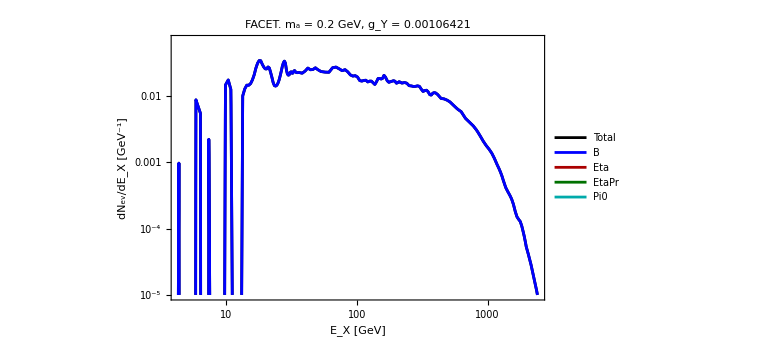

```mathematica
(*Variable = "E_X","z_X","θ_X". The number belongs to the column in the tabulated data*)
iVal:=Association[{"E_X" ->2,"θ_X"->1,"z_X"->3}]
Δxvals["E_X"]:=ΔEvals;
Δxvals["z_X"]=Δzvals;
Do[Δxvals["θ_X",prod]=Δθvals[prod],{prod,ProductionList}];
LegendX:=Association[{"E_X"->"E_X [GeV]","θ_X"->"θ_X [rad]","z_X"-> "z_X [m]"}]
LegendY:=Association[{"E_X"->"dN_ev/dE_X [GeV^-1]","θ_X"->"dN_ev/dθ_X [rad^-1]","z_X"-> "dN_ev/dz_X [m^-1]"}]
(*Differential number of events*)
NeventsDifferentialDiscretProd[m_,ProdChannel_,coupling_,Variable_]:=Module[{NpotTimesχval},
ival=iVal[Variable];
NpotTimesχval=NpotGivenExperiment*ProbLLP[m,coupling,ProdChannel];
tablegrid0=TableIntegrandDiscret[m,ProdChannel,"True"];
OutGridEfinalTemp=OutGridEnergy[N[m],ProdChannel];
ΔEvals=(Rest[10^OutGridEfinalTemp]-Most[10^OutGridEfinalTemp]);
Δxval=Δxvals[Variable];
cτVal=cτLLP[m,coupling];
brvis=BrVis[m];
ilist=DeleteDuplicates[{ival,1,2,3}];
tablegrid1=SortBy[{#[[ilist[[1]]]],#[[ilist[[2]]]],#[[ilist[[3]]]],#[[4]]}&/@tableGridPrefac[tablegrid0,m,cτVal,0.],{#[[1]],#[[2]],#[[3]]}&];
GridQuantity=tablegrid1[[All,1]]//DeleteDuplicates;
LengthPerVariable=Length[tablegrid1]/Length[GridQuantity];
tab1=NdiffCompiled[tablegrid1,GridQuantity,LengthPerVariable,NpotTimesχval*brvis];
Join[tab1[[All,{1}]],Partition[tab1[[All,2]]*Δxval^-1,1],2]
]
NeventsDifferentialDiscret[m_,coupling_,Variable_]:=Module[{NdiffInt,LegendList,QuantityMinMax,ValueMinMax},
prodlisttemp={};
Do[If[Max[mLLPmin[prod],mminϵ]<m<Min[mLLPmax[prod],mmaxϵ],
prodlisttemp=Join[prodlisttemp,{prod}];
NdiffData[prod]=NeventsDifferentialDiscretProd[m,prod,coupling,Variable];
XvalminmaxNdiff=Select[NdiffData[prod],#[[2]]>10^-40&][[All,1]]//MinMax;
NdiffInt[X_,prod]=If[XvalminmaxNdiff[[1]]<X<XvalminmaxNdiff[[2]],Evaluate[10^Interpolation[{Log10[#[[1]]],Log10[#[[2]]+10^-90]}&/@NdiffData[prod],InterpolationOrder->1][Log10[X]]],0]],{prod,ProductionList}];
NdiffInt[X_,"Total"]=Sum[NdiffInt[X,prod],{prod,prodlisttemp}];
LegendList=Join[{"Total"},prodlisttemp];
QuantityMinMax=Flatten[Table[MinMax[NdiffData[prod][[All,1]]],{prod,prodlisttemp}],1]//MinMax;
ValueMinMax=Max[Max[NdiffData[#][[All,2]]]&/@prodlisttemp];
{Table[NdiffInt[X,prod],{prod,LegendList}],LegendList,QuantityMinMax,ValueMinMax}
]
mvaltest=If[FacilityGivenExperiment=="ESS",0.04,0.2];
couplingvaltest=1.4LowerBoundEstimate[mvaltest,ProductionList[[1]]];
quantity="E_X";
{NdiffTab[X_],LegendList,QuantityMinMax,ValueMinMax}=NeventsDifferentialDiscret[mvaltest,couplingvaltest,quantity];
Do[
prch=LegendList[[i]];
NdiffInt[X_,prch]=NdiffTab[X][[i]];
,{i,1,Length[LegendList]}];
plotdiff=LogLogPlot[Evaluate[Table[NdiffInt[X,prod],{prod,LegendList}]],{X,QuantityMinMax[[1]],QuantityMinMax[[2]]},Frame->True,ImageSize->Large,PlotRange->{All,{10^-5,2ValueMinMax}},PlotStyle->{{Thick,Black},{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Darker@Green},{Thick,Darker@Cyan},{Thick,Magenta},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]}},PlotLegends->Placed[Style[#,20]&/@LegendList,Right],FrameLabel->{LegendX[quantity] ,LegendY[quantity]},FrameStyle->Directive[Black, 18],PlotLabel->Style[Row[{SelectedExperiment,". m_a = ",mvaltest," GeV, g_Y = ",couplingvaltest//N}],14,Black]]
```

# Exporting tabulated number of events

## Definitions

```mathematica
directory["Nevents"]=FileNameJoin[{NotebookDirectory[],"Tabulated Nevents"}];
directory["Nevents-LLP"]=FileNameJoin[{NotebookDirectory[],"Tabulated Nevents",LLPdirName}];
directory["Nevents-LLP-experiment"]=FileNameJoin[{NotebookDirectory[],"Tabulated Nevents",LLPdirName,SelectedExperiment}];
If[!DirectoryQ[directory[#]],CreateDirectory[directory[#]]]&/@{"Nevents","Nevents-LLP","Nevents-LLP-experiment"};
Print["Filenames with tabulated N_events:"]
Do[FilenameNevents[prod]=ToString@StringForm["Nevents_``_``_at_``_Npot=``.dat",Sequence@@{LLPdirName,prod,SelectedExperiment,NpotGivenExperiment//CForm//ToString}],{prod,ProductionList}]
FilenameNevents[#]&/@ProductionList
Do[mRangeExport[prod]={0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.151,0.2,0.21,0.215,0.218,0.22,0.225,0.23,0.24,0.25,0.27,0.301,0.35,0.4,0.425,0.45,0.47,0.5,0.51,0.52,0.53,0.535,0.54,0.543,0.544,0.545,0.546,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.67,0.7,0.725,0.75,0.77,0.8,0.825,0.85,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.953,0.954,0.955,0.956,0.96,0.961,0.962,0.963,0.966,0.97,0.973,0.975,0.98,1.,1.01,1.02,1.03,1.05,1.07,1.1,1.12,1.15,1.2,1.25,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.9,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.76}//N;
,{prod,ProductionList}]
couplingsRangeExport=Table[10^x,{x,-7,-1,0.017}]//N;
```

Filenames with tabulated N_events:

{Nevents_ALP-fermion_B_at_FACET_Npot=2.16e17.dat,Nevents_ALP-fermion_DrellYan_at_FACET_Npot=2.16e17.dat,Nevents_ALP-fermion_Eta_at_FACET_Npot=2.16e17.dat,Nevents_ALP-fermion_EtaPr_at_FACET_Npot=2.16e17.dat,Nevents_ALP-fermion_Pi0_at_FACET_Npot=2.16e17.dat}

## Exporting

## Common definition

```mathematica
BlockExport[ProdChannel_]:=Module[{mlist},
mlist=mRangeExport[ProdChannel];
TabFrom=ParallelTable[Quiet[NeventsDiscret[mlist[[k]],ProdChannel,couplingsRangeExport]],{k,1,Length[mlist],1}];
Export[FileNameJoin[{directory["Nevents-LLP-experiment"],FilenameNevents[ProdChannel]}],Flatten[TabFrom,1],"Table"]
]
Monitor[
Do[
prod=ProductionList[[j]];
BlockExport[prod],{j,1,Length[ProductionList],1}],
Row[{ProgressIndicator[j,{1,Length[ProductionList]}]," Production mode = ",ProductionList[[j]]," (", j,"/",Length[ProductionList],")"}]]//AbsoluteTiming
If[icounter>Length[SelectedExperimentList],BlockEvaluation["Sensitivity"]]
```

{69.1544,Null}

# Computing sensitivities

## Basic definitions

```mathematica
LLPdirName="ALP-fermion";
directory["Sensitivity"]=FileNameJoin[{NotebookDirectory[],"Sensitivity domains"}];
directory["Sensitivity-LLP"]=FileNameJoin[{directory["Sensitivity"],LLPdirName}];
If[!DirectoryQ[directory[#]],CreateDirectory[directory[#]]]&/@{"Sensitivity","Sensitivity-LLP"};
directory["Nevents-LLP"]=FileNameJoin[{NotebookDirectory[],"Tabulated Nevents",LLPdirName}];
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
infoDialog[phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],Button["Proceed",DialogReturn[choice]]}]]
selectionDialog[list_,phrase_]:=DialogInput[{choice={}},Column[{Row[{phrase}],Pane[TogglerBar[Dynamic[choice],list,Appearance->"Vertical"->{Automatic,5}],ImageSize->{Automatic,Automatic},Scrollbars->{False,True}],Button["OK",DialogReturn[choice]]}]]
ExperimentDirectoriesListNevents=Select[FileNames["*",directory["Nevents-LLP"],1],DirectoryQ];
Print["List of available experiments with tabulated N_events for " <>LLPdirName<>":"]
ExperimentsListNevents=Table[FileNameTake[ExperimentDirectoriesListNevents[[i]],-1],{i,1,Length[ExperimentDirectoriesListNevents],1}]//Sort;
ExperimentsListNevents//TableForm
If[Length[ExperimentsListNevents]==0,Print["No experiment is available, generate first the acceptance for the given experiment using module 1"],
SelectedExperimentList=If[Length[ExperimentsListNevents]≠0,selectionDialog[ExperimentsListNevents,"Select the experiments for which the sensitivity will be computed:"]];
icounter=1;
BlockEvaluation[tag_]:=Block[{},
nb=EvaluationNotebook[];
NotebookFind[nb,tag,All,CellTags];
SelectionEvaluate[nb]
];
Do[
BlockEvaluation["Sensitivity-computation"];
,{icounter,1,Length[SelectedExperimentList],1}]
]
```

List of available experiments with tabulated N_events for ALP-fermion:

CODEX-b
DarkQuest-phase-2
FACET
SHIFT-muon
SHiP-ECN4

## Specifying the experiment and interpolating the tabulated number of events

## Selecting the experiment

```mathematica
Print["Selected experiment:"]
GivenExperimentForSensitivityComputation=SelectedExperimentList[[icounter++]]
CondANUBIS=MemberQ[{"ANUBIS-shaft-volume-1","ANUBIS-shaft-volume-2","ANUBIS-shaft-volume-3"},GivenExperimentForSensitivityComputation];
If[CondANUBIS==True,infoDialog[Row[{"One of the modules of ANUBIS-shaft is chosen. The full sensitivity includes three modules. The importing will be over all modules, so for all ot the the sensitivity has to be computed"}]]]
If[CondANUBIS==False,GivenExperimentForSensitivityComputationList={GivenExperimentForSensitivityComputation},GivenExperimentForSensitivityComputationList={"ANUBIS-shaft-volume-1","ANUBIS-shaft-volume-2","ANUBIS-shaft-volume-3"}];
directoriesNeventsSelected={};
Do[directoriesNeventsSelected=Join[directoriesNeventsSelected,FileNames["*.dat",FileNameJoin[{directory["Nevents-LLP"],exp}]]],{exp,GivenExperimentForSensitivityComputationList}];
(*Creating the directory for exporting sensitivity curves*)
ExperimentFolder=If[CondANUBIS==True,"ANUBIS",GivenExperimentForSensitivityComputation];
directory["Sensitivity-LLP-exp"]=FileNameJoin[{directory["Sensitivity-LLP"],ExperimentFolder}];
If[!DirectoryQ[directory["Sensitivity-LLP-exp"]],CreateDirectory[directory["Sensitivity-LLP-exp"]]]
```

Selected experiment:

FACET

/Users/jeremi/Documents/Physics/SHIFT/SensCalc.nosync/Sensitivity domains/ALP-fermion/FACET

## Importing and interpolations

List of production channels:

Mother | Experiment | N_PoT
B | FACET | 2.16e17
DrellYan | FACET | 2.16e17
Eta | FACET | 2.16e17
EtaPr | FACET | 2.16e17
Pi0 | FACET | 2.16e17

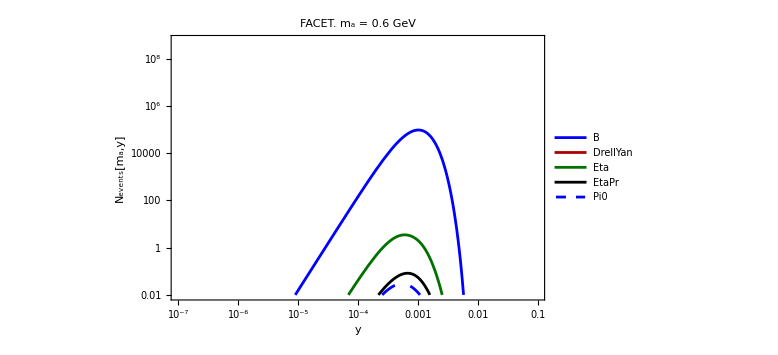

```mathematica
Print["List of production channels:"]
FilenamesNevents=Table[Last@FileNameSplit@directoriesNeventsSelected[[i]],{i,1,Length[directoriesNeventsSelected],1}];
FilenameParameters[i_]:=StringCases[FilenamesNevents[[i]],"Nevents_"<>LLPdirName<>"_"~~mother__~~"_at_"~~experiment__~~"_Npot="~~Npot__~~".dat":>{mother,experiment,Npot}][[1]]
(*______________________________________________________*)
(*Importing and interpolation*)
(*______________________________________________________*)
ProductionInfoList=Table[FilenameParameters[i],{i,1,Length[FilenamesNevents],1}];
Join[{{"Mother","Experiment","N_PoT"}},ProductionInfoList]//TableForm
ProductionChannelsList=ProductionInfoList[[All,1]];
NpotDefault=Interpreter["Number"][ProductionInfoList[[1]][[3]]];
NeventsTabulated//Clear;
ϵreco[mLLP_]=1;
If[StringContainsQ[GivenExperimentForSensitivityComputation,"LHCb-downstream"],
ϵreco[mLLP_]=0.4];
If[StringContainsQ[GivenExperimentForSensitivityComputation,"CHARM-lepton"],ϵreco[mLLP_]=If[mLLP<0.105*2,0.51,0.85]];
If[StringContainsQ[GivenExperimentForSensitivityComputation,"NuCal"],ϵreco[mLLP_]=If[mLLP<0.105*2,0.7,0.8]];
Do[
Module[{prod},
prod=ProductionChannelsList[[i]];
(*The condition if one sums the number of events for the same production mode over several experiments*)
IfprodExists=MemberQ[Keys[DownValues@NeventsTabulated][[All,1,1]],prod];
NeventsTabulated[prod]=If[!IfprodExists,Import[directoriesNeventsSelected[[i]],"Table"],Join[NeventsTabulated[prod][[All,{1,2}]],NeventsTabulated[prod][[All,{3}]]+Import[directoriesNeventsSelected[[i]],"Table"][[All,{3}]]]];
{mminmax[prod],couplingminmax[prod]}=(NeventsTabulated[prod][[All,#]]//MinMax)&/@{1,2};
NevMax[prod]=NeventsTabulated[prod][[All,3]]//Max;
NevInt[mLLP_,y_,prod]=ϵreco[mLLP]*If[mminmax[prod][[1]]≤ mLLP≤mminmax[prod][[2]]&&couplingminmax[prod][[1]]≤y≤couplingminmax[prod][[2]],Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@NeventsTabulated[prod],InterpolationOrder->1][Log10[mLLP],Log10[y]])],0];
]
,{i,1,Length[ProductionInfoList],1}]
{mminmaxOverall,couplingminmaxOverall}=MinMax[Table[#[prod],{prod,ProductionChannelsList}]//Flatten]&/@{mminmax,couplingminmax};
NevMaxOverall=Max[Table[NevMax[prod],{prod,ProductionChannelsList}]];
NevIntOverall[mLLP_,y_]=Sum[NevInt[mLLP,y,prod],{prod,ProductionChannelsList}];
pt[mLLP_]:=LogLogPlot[Evaluate[Table[NevInt[mLLP,y,prod],{prod,ProductionChannelsList}]],{y,couplingminmaxOverall[[1]],couplingminmaxOverall[[2]]},PlotLegends->Placed[Style[#,15]&/@ProductionChannelsList,Right],PlotRange->{couplingminmaxOverall,{10^-2,NevMaxOverall}},Frame->True,ImageSize->Large,FrameLabel->{"y" , "N_events[m_a,y]"},FrameStyle->Directive[Black, 23],PlotStyle->{{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Darker@Green},{Thick,Black},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Black,Dashing[0.02]}},PlotLabel->Style[Row[{GivenExperimentForSensitivityComputation,". m_a = ",mLLP, " GeV"}],20,Black]]
pt[0.6]
```

## Sensitivity computation

## N_events density plot

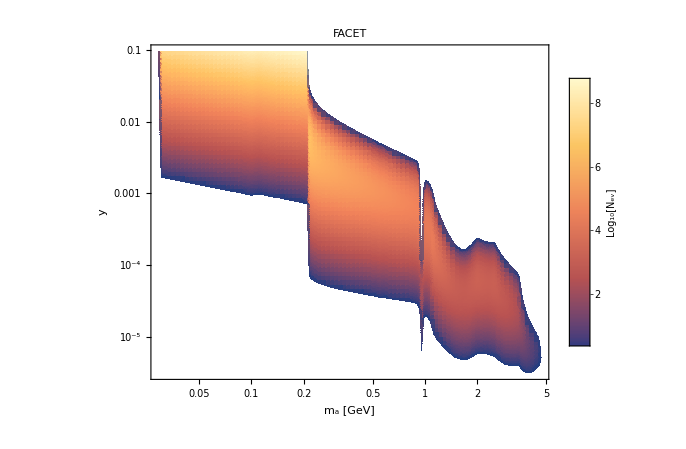

```mathematica
plot=DensityPlot[Evaluate[Log10[NevIntOverall[mLLP,y]]],{mLLP,mminmaxOverall[[1]],mminmaxOverall[[2]]},{y,couplingminmaxOverall[[1]],couplingminmaxOverall[[2]]},ScalingFunctions->{"Log","Log"},AspectRatio->0.78,PlotRange->{All,All,{Log10[2.3],Log10[NevMaxOverall]}},ImageSize->Large,FrameLabel->{"m_a [GeV]","y"}, Frame-> True, FrameStyle->Directive[Black, 25],PlotPoints->100,PlotLegends->Placed[BarLegend[{Automatic,{Log10[2.3],Log10[NevMaxOverall]}},LegendMarkerSize->340,LegendLabel->Placed["Log_10[N_ev]",Bottom],LabelStyle->{FontSize->22},Method->{FrameStyle->Black,AxesStyle->None,TicksStyle->Black}],Right],PlotLabel->Style[Row[{ExperimentFolder}],20,Black](*,FrameTicks->{{Automatic,Automatic},{TicksPlotx,None}}*)]
(*Export[FileNameJoin[{NotebookDirectory[],"plots/SensCalc/NeventsDensityPlotExample.pdf"}],plot,"AllowRasterization"->False]*)
```

## Constraints importing

```mathematica
importformat["txt"]=importformat["dat"]="Table";
importformat["m"]=importformat["mx"]="MX";
importformat["xls"]="XLS";
dir=FileNameJoin[{NotebookDirectory[],"contours",LLPdirName}];
If[DirectoryQ[dir],
filenames=FileNames[LLPdirName<>"-excluded*",dir,Infinity];
ExcludedRegions[LLPdirName]=Import[#,importformat[FileExtension[#]]]&/@FileNames[LLPdirName<>"-excluded*",dir,Infinity];
];
If[!DirectoryQ[dir],
ExcludedRegions[LLPdirName]={{{10.,10.}}};
]
```

## Sensitivity

N_PoT for computation | N_(ev, min) | Selected production modes
2.16×10^17 | 2.3 | B
DrellYan
Eta
EtaPr
Pi0

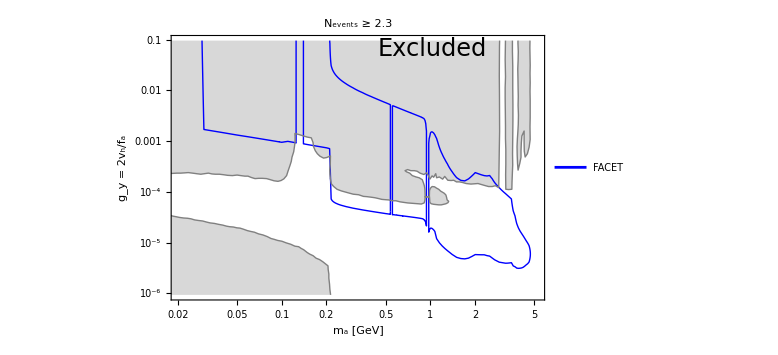

```mathematica
SensitivityBlock[Nev_,Npot_,SelectedProduction_]:=Block[{},
NevTot[mLLP_,y_]=Sum[NevInt[mLLP,y,prod],{prod,SelectedProduction}];
RegSens1=RegionPlot[Npot/NpotDefault NevTot[10^mLLP,10^ga]*Boole[!(0.125<10^mLLP<0.14||0.538<10^mLLP<0.555||0.94<10^mLLP<0.974)]≥Nev,{mLLP,Log10[mminmaxOverall[[1]]],Log10[0.125]},{ga,Log10[couplingminmaxOverall[[1]]],Log10[couplingminmaxOverall[[2]]]},PlotPoints->200];
RegSens2=RegionPlot[Npot/NpotDefault NevTot[10^mLLP,10^ga]*Boole[!(0.125<10^mLLP<0.14||0.538<10^mLLP<0.555||0.94<10^mLLP<0.974)]≥Nev,{mLLP,Log10[0.14],Log10[0.538]},{ga,Log10[couplingminmaxOverall[[1]]],Log10[couplingminmaxOverall[[2]]]},PlotPoints->200];
RegSens3=RegionPlot[Npot/NpotDefault NevTot[10^mLLP,10^ga]*Boole[!(0.125<10^mLLP<0.14||0.538<10^mLLP<0.555||0.94<10^mLLP<0.974)]≥Nev,{mLLP,Log10[0.538],Log10[0.94]},{ga,Log10[couplingminmaxOverall[[1]]],Log10[couplingminmaxOverall[[2]]]},PlotPoints->200];
RegSens4=RegionPlot[Npot/NpotDefault NevTot[10^mLLP,10^ga]*Boole[!(0.125<10^mLLP<0.14||0.538<10^mLLP<0.555||0.94<10^mLLP<0.974)]≥Nev,{mLLP,Log10[0.974],Log10[mminmaxOverall[[2]]]},{ga,Log10[couplingminmaxOverall[[1]]],Log10[couplingminmaxOverall[[2]]]},PlotPoints->200];
(*Sens={10^#[[1]],10^#[[2]]}&/@Partition[Flatten[Cases[Normal@RegSens,Line[x_]:>x,Infinity]],2];*)
SensTemp=Cases[Normal@#,Line[x_]:>x,Infinity]&/@{RegSens1,RegSens2,RegSens3,RegSens4};
SensTemp1=Join[SensTemp[[1]],SensTemp[[2]],SensTemp[[3]],SensTemp[[4]]];
Sens=Table[{10^#[[1]],10^#[[2]]}&/@SensTemp1[[i]],{i,1,Length[SensTemp1],1}];
Export[FileNameJoin[{directory["Sensitivity-LLP-exp"],ToString@StringForm["Sensitivity_``_at_``_Nev=``_Npot=``.xls",Sequence@@{LLPdirName,ExperimentFolder,Nev//ToString,Npot//CForm//ToString}]}],Sens];
Sens
]
productionlist=Join[{"All"},ProductionChannelsList];
DynamicModule[{input1=NpotDefault,input2=2.3,choice={"All"},list,phrase},
DialogInput[Column[{Style[GivenExperimentForSensitivityComputation,Bold],TextCell["Enter the number of proton collisions:"],InputField[Dynamic[input1],Expression],TextCell["Enter the value of N_ev,min for which the sensitivity will be computed:"],InputField[Dynamic[input2],Expression],Row[{"Select the production channels to be used for the sensitivity calculation:"}],Pane[TogglerBar[Dynamic[choice],productionlist,Appearance->"Vertical"->{Automatic,1}],ImageSize->{Automatic,Automatic},Scrollbars->{False,True}],Button["Submit",DialogReturn[{NpotVal,NevMinVal,SelectedProduction}={input1,input2,choice}//N],ImageSize->Automatic]}]]];
If[MemberQ[SelectedProduction,"All"],SelectedProduction=ProductionChannelsList;]
{{"N_PoT for computation","N_(ev, min)","Selected production modes"},{NpotVal,NevMinVal,SelectedProduction}}//TableForm
sens=SensitivityBlock[NevMinVal,NpotVal,SelectedProduction];
Show[ListLogLogPlot[Cases[{sens,ExcludedRegions[LLPdirName]},_?MatrixQ,All],Joined->{True,True,True,True},Frame-> True,FrameLabel->{"m_a [GeV]" , "g_y = 2v_h/f_a"},FrameStyle->Directive[Black, 23],PlotStyle->Flatten[{ConstantArray[{Thick,Blue},If[MatrixQ[sens],1,Length@sens]],ConstantArray[{Thick,Gray},If[MatrixQ[ExcludedRegions[LLPdirName]],1,Length@ExcludedRegions[LLPdirName]]]},1],Filling->{Length[sens]+1->{True,Directive[Gray,Opacity[0.3]]},Length[sens]+2->{True,Directive[Gray,Opacity[0.3]]},Length[sens]+3->{True,Directive[Gray,Opacity[0.3]]},Length[sens]+4->{True,Directive[Gray,Opacity[0.3]]}},ImageSize->Large,PlotRange->{{1.01mminmaxOverall[[1]],1.1mminmaxOverall[[2]]},{0.3Min[Flatten[Sens]],0.99couplingminmaxOverall[[2]]}},PlotLabel->Style[Row[{"N_events ≥ ",NevMinVal}],18,Black],PlotLegends->Placed[Style[#,15]&/@{ExperimentFolder},{0.2,0.15}]](*,LogLogPlot[{x,x^2,x^3,x^4,x^5,x^6},{x,0.05,62.49},PlotStyle->{{Thickness[0.006],Blue},{Thickness[0.006],Darker@Red},{Thickness[0.006],Darker@Red,Dashing[0.02]},{Thickness[0.006],Black},{Thickness[0.01],Darker@Cyan,Dashing[0.007]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Darker@Red}},PlotLegends->Placed[Style[#,15]&/@{"SHiP","SHADOWS_(specified in LoI)","SHADOWS_(specified by Gaia)", "SHADOWS_(collab estimate)"},{0.26,0.15}]]*),Graphics[{Text[Style["Excluded",24,Black],Scaled[{0.7,0.95}]]}]]
```

# Deleting generated cells

```mathematica
FrontEndTokenExecute["DeleteGeneratedCells"];
FrontEndTokenExecute["SelectAll"];
FrontEndTokenExecute["SelectionCloseAllGroups"];
```